kmr formalism in kt factorization framwork.(e+e-)

Setting up the first parts

```mathematica
Clear["Global *"]
```

AlphaS.-Graphics-

```mathematica
nf=5;
LamQCD=0.5;
beta0=11.-nf 2./3.;
beta1=102.-nf 38./3.;
AlphaS[mu2_]=4 Pi/beta0/Log[mu2/LamQCD^2]  ;
```

Setting up constant parameters, color factors, etc.

```mathematica
CF = 1.3333 ;
CA=3;
TF = 0.5;(*k factor*)
```

Setting up the sudakov form factors (virtual (loop) contributions ) in KMR approch.(survival probability)
-Graphics-
P_qg(1-z)=P_qg(z)

```mathematica
zmax[k2_,mu2_,z_]:=((Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2 k2]));
zmin[k2_,mu2_]:=(Sqrt[k2])/(Sqrt[mu2]+Sqrt[k2]);
Subscript[P, qg][z_]:=TF(z^2+(1-z)^2);
Subscript[P, qq][z_]:=CF((1+z^2)/(1-z));
Subscript[P, gg][z_]:=2CA(z/(1-z)+(1-z)/z+z(1-z));Subscript[P, gq][z_]:=CF((1+(1-z)^2)/z);
```

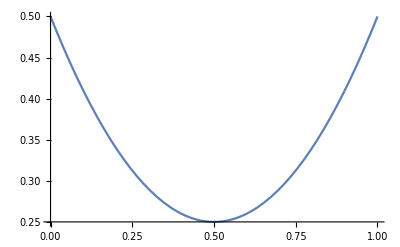

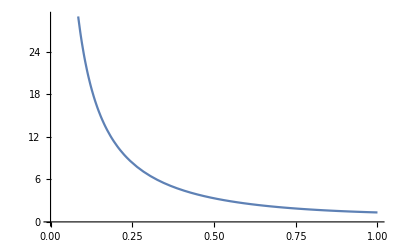

```mathematica
Plot[TF(z^2+(1-z)^2), {z,0,1}]
Plot[CF((1+(1-z)^2)/z), {z,0,1}]
```

```mathematica
Dhtotal[z_,mu2_]=(Duh[z,mu2]);
UDtotal[z_,mu2_,kt2_]:=NIntegrate[  Subscript[P, gq][x]*Dgh[z/x,kt2],{x,z,((Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2 kt2]))}];
UDtotal[z,mu2,kt2]/.mu2->50/.z-> 0.1;
kkk5[kt2_]=%;Clear[result100];result100 = {};
result100= Flatten[Table[{{1j,kkk5[1j*1j]}},{j,1,100}],1]
```

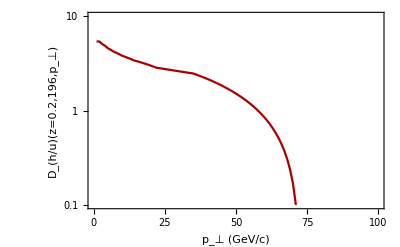

```mathematica
M100umrw=ListLogPlot[result100,Joined->True,PlotStyle->{Darker[Red]},Frame->True,PlotRange-> {{0,100},{0.1,10}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV/c)","D_(h/u)(z=0.2,196,p_⊥)"}]
```

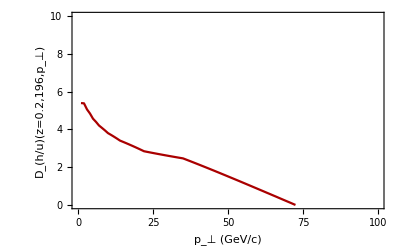

```mathematica
M100umrw=ListPlot[result100,Joined->True,PlotStyle->{Darker[Red]},Frame->True,PlotRange-> {{0,100},{0.0001,10}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV/c)","D_(h/u)(z=0.2,196,p_⊥)"}]
```

```mathematica
UDtotal[z_,kt2_]=NIntagrate[Subscript[P, qg][x]Dgh[z/x,kt2],{x,z,1}]
UDtotal[z,x,kt2]/.z-> 0.6;
kkk5[kt2_]=%;Clear[result100];result100 = {};
result100= Flatten[Table[{{0.1j,kkk5[0.1j*0.1j]}},{j,10,200}],1]
```

NIntagrate[0.5 ((1-x)^2+x^2) InterpolatingFunction[…][z/x,kt2],{x,z,1}]

```mathematica
Subscript[T, q][kt2_, mu2_,z_]:=Exp[-NIntegrate[AlphaS[k2]/(2*Pi*k2)(( CF *(-1/6 ((Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2 k2]))(12+((Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2 k2])) (3+2 ((Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2 k2]))))-2 Log[1-((Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2 k2]))]))+1/3*TF),{k2,kt2,mu2}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k2 near {k2} = {0.273415}. NIntegrate obtained 2.71253 and 8.619 for the integral and error estimates.

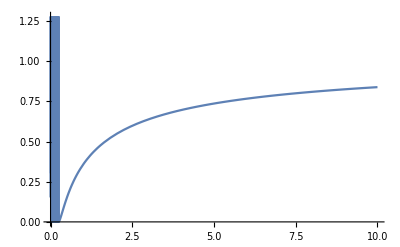

```mathematica
Plot[Subscript[T, q][kt2, 100,0.6],{kt2,0,10}]
```

Read and interpolate DSS fragm. fns.  (Q^2 from 196 to 1936 GeV^2) - 
Note that this are moments, i.e. z*D(z,Q) - 
Fragmentation functions for h+ + h-  from DSS LO set

```mathematica
SetDirectory["D:\\3 [07]\\E derive\\postdoc\\project tehran uni"];
```

```mathematica
Clear[DSSh,Duh,Ddh,Dsh,Dch,Dgh]
```

```mathematica
DSSh= ReadList["ff8.dat",Real,RecordLists-> True];
```

```mathematica
Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,3]]},{i,1,Length[DSSh]}];
```

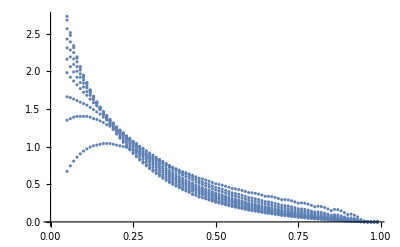

```mathematica
ListPlot[Table[{DSSh[[i,1]],DSSh[[i,3]]},{i,1,Length[DSSh]}]]
```

```mathematica
Duh=Interpolation[Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,3]]},{i,1,Length[DSSh]}]];
Ddh=Interpolation[Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,4]]},{i,1,Length[DSSh]}]];
Dsh=Interpolation[Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,5]]},{i,1,Length[DSSh]}]];
Dch=Interpolation[Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,6]]},{i,1,Length[DSSh]}]];Dbh=Interpolation[Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,7]]},{i,1,Length[DSSh]}]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Dgh=Interpolation[Table[{{DSSh[[i,1]],DSSh[[i,2]]},DSSh[[i,8]]},{i,1,Length[DSSh]}]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

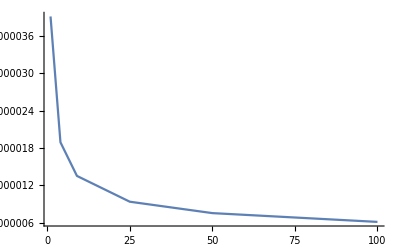

```mathematica
Plot[{Duh[0.99,Q]},{Q,1,100},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
Plot[{Dgh[z,1936]},{z,0.01,0.9},AxesOrigin->{0,0}]
```

```mathematica
Dgh[1,1936]
```

-1.6433×10^-6

UFFs: like:   -Graphics-

```mathematica
Dhtotal[z_,mu2_]=(Duh[z,mu2]);
UDtotal[z_,mu2_,kt2_]:=Subscript[T, q][kt2,mu2,z](AlphaS[kt2]/(2Pi))NIntegrate[ Subscript[P, qq][x]*Dhtotal[z/x,kt2],{x,z,(Sqrt[mu2])/(Sqrt[mu2]+Sqrt[z^2*kt2])}]+Subscript[T, q][kt2,mu2,z](AlphaS[kt2]/(2Pi))NIntegrate[  Subscript[P, gq][x]*Dgh[z/x,kt2],{x,z,1}];
```

```mathematica
UDtotal[z,mu2,kt2]/.mu2->100/.z-> 0.6;
kkk5[kt2_]=%;Clear[result100];result100 = {};
result100= Flatten[Table[{{0.1j,kkk5[0.1j*0.1j]}},{j,10,200}],1]
```

NIntegrate::nlim: k2 = kt2 z^2 is not a valid limit of integration.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::nlim: k2 = 0.36 kt2 is not a valid limit of integration.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::nlim: k2 = 0.36 kt2 is not a valid limit of integration.

NIntegrate::nlim: x = 10./(10.+0.6 √kt2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.667181}. NIntegrate obtained 0.679965 and 1.33588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.706244}. NIntegrate obtained 0.651883 and 1.30006×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.644525}. NIntegrate obtained 0.621025 and 3.2462×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.,0.0217175},{1.1,0.0322289},{1.2,0.0390628},{1.3,0.0429972},{1.4,0.0447542},{1.5,0.0448729},{1.6,0.0437463},{1.7,0.0416652},{1.8,0.0388521},{1.9,0.0354666},{2.,0.0316247},{2.1,0.030522},{2.2,0.0293239},{2.3,0.0280603},{2.4,0.0267552},{2.5,0.0254246},{2.6,0.0240796},{2.7,0.022728},{2.8,0.0213762},{2.9,0.0200218},{3.,0.0186654},{3.1,0.0179503},{3.2,0.0172512},{3.3,0.0165694},{3.4,0.0159055},{3.5,0.0152608},{3.6,0.0146354},{3.7,0.0140289},{3.8,0.0134416},{3.9,0.0128734},{4.,0.0123237},{4.1,0.011792},{4.2,0.0112776},{4.3,0.0107745},{4.4,0.0102817},{4.5,0.00979917},{4.6,0.0093276},{4.7,0.00886674},{4.8,0.00841679},{4.9,0.00797818},{5.,0.00755043},{5.1,0.00731743},{5.2,0.00709397},{5.3,0.00687962},{5.4,0.00667399},{5.5,0.00647682},{5.6,0.00628738},{5.7,0.00610279},{5.8,0.00592227},{5.9,0.00574593},{6.,0.00557442},{6.1,0.00540766},{6.2,0.00524566},{6.3,0.00508851},{6.4,0.00493616},{6.5,0.00478851},{6.6,0.00464539},{6.7,0.0045067},{6.8,0.00437222},{6.9,0.00424169},{7.,0.00411458},{7.1,0.0040033},{7.2,0.00392864},{7.3,0.00385542},{7.4,0.00378425},{7.5,0.00371508},{7.6,0.00364803},{7.7,0.00358335},{7.8,0.00352095},{7.9,0.00346076},{8.,0.00340282},{8.1,0.00334704},{8.2,0.00329316},{8.3,0.00324122},{8.4,0.00319088},{8.5,0.00314122},{8.6,0.00309215},{8.7,0.00304383},{8.8,0.00299648},{8.9,0.00295016},{9.,0.00290481},{9.1,0.00286039},{9.2,0.00281695},{9.3,0.0027746},{9.4,0.00273331},{9.5,0.00269306},{9.6,0.00265328},{9.7,0.0026139},{9.8,0.00257479},{9.9,0.00253573},{10.,0.0024967},{10.1,0.00248014},{10.2,0.00246364},{10.3,0.00244719},{10.4,0.00243075},{10.5,0.00241431},{10.6,0.00239785},{10.7,0.00238136},{10.8,0.00236485},{10.9,0.00234831},{11.,0.00233174},{11.1,0.00231513},{11.2,0.0022985},{11.3,0.00228182},{11.4,0.00226512},{11.5,0.00224838},{11.6,0.00223161},{11.7,0.0022148},{11.8,0.00219795},{11.9,0.00218106},{12.,0.00216413},{12.1,0.00214717},{12.2,0.00213016},{12.3,0.00211311},{12.4,0.00209602},{12.5,0.00207889},{12.6,0.00206171},{12.7,0.00204449},{12.8,0.00202723},{12.9,0.00200992},{13.,0.00199256},{13.1,0.00197515},{13.2,0.0019577},{13.3,0.0019402},{13.4,0.00192265},{13.5,0.00190505},{13.6,0.00188739},{13.7,0.00186969},{13.8,0.00185193},{13.9,0.00183412},{14.,0.00181626},{14.1,0.0018088},{14.2,0.00180134},{14.3,0.00179396},{14.4,0.00178659},{14.5,0.00177922},{14.6,0.00177185},{14.7,0.00176449},{14.8,0.00175713},{14.9,0.00174977},{15.,0.0017424},{15.1,0.00173505},{15.2,0.00172769},{15.3,0.00172033},{15.4,0.00171297},{15.5,0.00170561},{15.6,0.00169825},{15.7,0.00169089},{15.8,0.00168352},{15.9,0.00167616},{16.,0.00166879},{16.1,0.00166142},{16.2,0.00165405},{16.3,0.00164668},{16.4,0.0016393},{16.5,0.00163192},{16.6,0.00162454},{16.7,0.00161715},{16.8,0.00160976},{16.9,0.00160236},{17.,0.00159497},{17.1,0.00158756},{17.2,0.00158015},{17.3,0.00157274},{17.4,0.00156532},{17.5,0.00155789},{17.6,0.00155046},{17.7,0.00154303},{17.8,0.00153558},{17.9,0.00152814},{18.,0.00152068},{18.1,0.00151322},{18.2,0.00150575},{18.3,0.00149827},{18.4,0.00149079},{18.5,0.0014833},{18.6,0.0014758},{18.7,0.00146829},{18.8,0.00146078},{18.9,0.00145325},{19.,0.00144572},{19.1,0.00143818},{19.2,0.00143063},{19.3,0.00142307},{19.4,0.0014155},{19.5,0.00140792},{19.6,0.00140034},{19.7,0.00139275},{19.8,0.00138514},{19.9,0.00137753},{20.,0.0013699}}

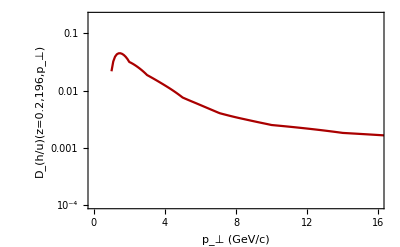

```mathematica
M100umrw=ListLogPlot[result100,Joined->True,PlotStyle->{Darker[Red]},Frame->True,PlotRange-> {{0,16},{0.0001,0.2}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV/c)","D_(h/u)(z=0.2,196,p_⊥)"}]
```

```mathematica
UDtotal[z,mu2,kt2]/.mu2->500/.z-> 0.6;
kkk5[kt2_]=%;Clear[result500];result500 = {};
result500 = Flatten[Table[{{0.5j,kkk5[0.5j*0.5j]}},{j,2,40}],1]
```

NIntegrate::nlim: k2 = kt2 is not a valid limit of integration.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::nlim: k2 = kt2 is not a valid limit of integration.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::nlim: k2 = kt2 is not a valid limit of integration.

NIntegrate::nlim: x = 22.3607/(22.3607+0.6 √kt2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.667181}. NIntegrate obtained 0.679965 and 1.33588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.706244}. NIntegrate obtained 0.511506 and 2.38231×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.706244}. NIntegrate obtained 0.227817 and 4.82797×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1.,0.0900649},{1.5,0.0829662},{2.,0.0573498},{2.5,0.0466996},{3.,0.0362558},{3.5,0.0306714},{4.,0.0256851},{4.5,0.0212362},{5.,0.0172516},{5.5,0.0149725},{6.,0.0129805},{6.5,0.0112213},{7.,0.00963523},{7.5,0.00851617},{8.,0.00757187},{8.5,0.00673374},{9.,0.00598629},{9.5,0.00531605},{10.,0.00470157},{10.5,0.0042884},{11.,0.00391756},{11.5,0.00358562},{12.,0.003289},{12.5,0.00302374},{13.,0.00277964},{13.5,0.00255278},{14.,0.00234334},{14.5,0.0022112},{15.,0.00209396},{15.5,0.00199024},{16.,0.00189587},{16.5,0.00180715},{17.,0.00172549},{17.5,0.00165126},{18.,0.00158391},{18.5,0.00152299},{19.,0.00146709},{19.5,0.00141376},{20.,0.0013635}}

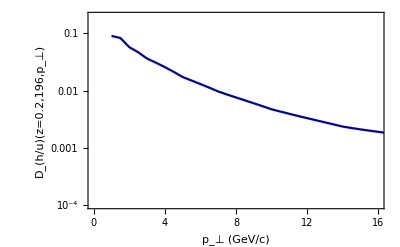

```mathematica
M500umrw=ListLogPlot[{{1.,0.09006488896260464},{1.5,0.08296620851556372},{2.,0.05734980207739089},{2.5,0.046699603845176955},{3.,0.03625580910092169},{3.5,0.030671438883828908},{4.,0.025685124598676966},{4.5,0.02123615478108382},{5.,0.017251636885825095},{5.5,0.014972482010966064},{6.,0.01298052877266358},{6.5,0.01122131554477779},{7.,0.009635225683931676},{7.5,0.008516167507576165},{8.,0.007571868923515381},{8.5,0.006733736604804151},{9.,0.005986294179007841},{9.5,0.0053160489634901265},{10.,0.004701574910245659},{10.5,0.00428840118285552},{11.,0.003917560995049893},{11.5,0.0035856211754332935},{12.,0.0032890005240452666},{12.5,0.0030237405630822696},{13.,0.002779644264142395},{13.5,0.002552775718254132},{14.,0.0023433442769871205},{14.5,0.002211203654633239},{15.,0.0020939566143715195},{15.5,0.001990242089347622},{16.,0.0018958726766358123},{16.5,0.0018071470228571516},{17.,0.001725485981095675},{17.5,0.001651257774296506},{18.,0.0015839069507057853},{18.5,0.001522987252491086},{19.,0.001467085748442843},{19.5,0.0014137581844997952},{20.,0.0013635047570430695}},Joined->True,PlotStyle->{Darker[Blue]},Frame->True,PlotRange-> {{0,16},{0.0001,0.2}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV/c)","D_(h/u)(z=0.2,196,p_⊥)"}]
```

```mathematica
UDtotal[z,mu2,kt2]/.mu2->1000/.z-> 0.6;
kkk5[kt2_]=%;Clear[result1000];result1000 = {};
result1000 = Flatten[Table[{{0.5j,kkk5[0.5j*0.5j]}},{j,2,40}],1]
```

NIntegrate::nlim: k2 = kt2 is not a valid limit of integration.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::nlim: k2 = kt2 is not a valid limit of integration.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::nlim: k2 = kt2 is not a valid limit of integration.

NIntegrate::nlim: x = 31.6228/(31.6228+0.6 √kt2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.6,1}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.667181}. NIntegrate obtained 0.679965 and 1.33588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.706244}. NIntegrate obtained 0.511506 and 2.38231×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.706244}. NIntegrate obtained 0.227817 and 4.82797×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1.,0.0724709},{1.5,0.0758276},{2.,0.0573583},{2.5,0.0492346},{3.,0.0400537},{3.5,0.0350169},{4.,0.0302846},{4.5,0.0258761},{5.,0.0217446},{5.5,0.0193104},{6.,0.0170956},{6.5,0.0150731},{7.,0.0132195},{7.5,0.0118812},{8.,0.0107295},{8.5,0.00968513},{9.,0.00873355},{9.5,0.00785452},{10.,0.00703811},{10.5,0.00646412},{11.,0.00593869},{11.5,0.00545767},{12.,0.00501685},{12.5,0.00461276},{13.,0.00424145},{13.5,0.00389849},{14.,0.00357683},{14.5,0.00334849},{15.,0.00313773},{15.5,0.00294356},{16.,0.00276501},{16.5,0.002601},{17.,0.00245049},{17.5,0.00231237},{18.,0.00218439},{18.5,0.0020634},{19.,0.00194962},{19.5,0.00184286},{20.,0.00174297}}

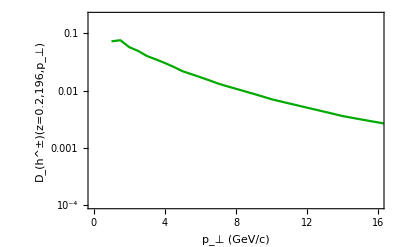

```mathematica
M1000umrw=ListLogPlot[{{1.,0.07247085663783642},{1.5,0.07582759565507198},{2.,0.05735825435400012},{2.5,0.049234635544834024},{3.,0.04005366060828731},{3.5,0.03501689608740893},{4.,0.030284596003357166},{4.5,0.025876079419597953},{5.,0.021744640504024984},{5.5,0.0193103922878289},{6.,0.017095639044891225},{6.5,0.015073148118115907},{7.,0.013219522275298167},{7.5,0.01188124680442442},{8.,0.010729461247066382},{8.5,0.009685125095105907},{9.,0.008733547473842855},{9.5,0.0078545211527352},{10.,0.0070381065783851685},{10.5,0.006464117127573468},{11.,0.005938692288326059},{11.5,0.005457667855716731},{12.,0.005016848718800071},{12.5,0.004612755318938265},{13.,0.00424145043080579},{13.5,0.003898486263164377},{14.,0.0035768253194248846},{14.5,0.003348490088759491},{15.,0.003137727652050533},{15.5,0.002943563589960755},{16.,0.0027650115100384294},{16.5,0.0026009986438355025},{17.,0.002450486879104512},{17.5,0.0023123696641541786},{18.,0.0021843914188757344},{18.5,0.002063398699009817},{19.,0.0019496243056318914},{19.5,0.0018428557897752053},{20.,0.0017429680215853862}},Joined->True,PlotStyle->{Darker[Green]},Frame->True,PlotRange-> {{0,16},{0.0001,0.2}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV/c)","D_(h^±)(z=0.2,196,p_⊥)"}]
```

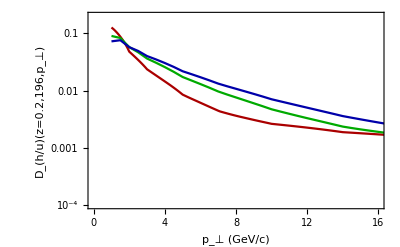

```mathematica
Show[M100umrw,M500umrw,M1000umrw]
```

```mathematica
Show[M100ukmr,M500ukmr,M1000ukmr,M100umrw,M500umrw,M1000umrw]
```

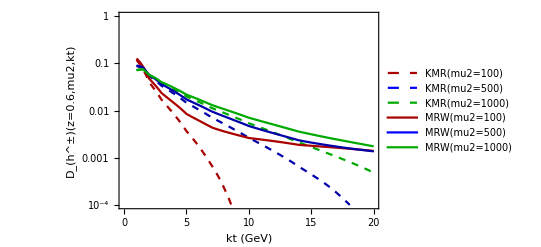

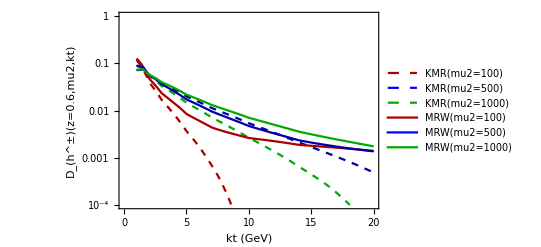

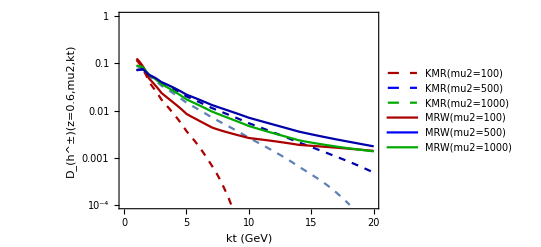

```mathematica
LineLegend[{{Darker[Red]},{Green,Dashed},{Blue,DotDashed},{Brown,Dotted},Brown},{"","",""}]
LineLegend[{{Darker[Red],Dashed},{Blue,Dashed},{Darker[Green],Dashed},Brown},{"KMR(mu2=100)","KMR(mu2=500)","KMR(mu2=1000)"}]
LineLegend[{{Darker[Red]},{Blue},{Darker[Green]},Brown},{"MRW(mu2=100)","MRW(mu2=500)","MRW(mu2=1000)"}]
LineLegend[{{Purple},Brown},{"FEWZ (MSTW008)"}]
```

data of 1/σ_0dσ/dp_t, mu=14; TASSO

```mathematica
SIntegrant[z_]=0.0018 mu2^0.727*(2*Pi)/Sqrt[kt2]*UDtotal[z,mu2,kt2]/z;
Subscript[z, 0]=a;b=(0.8);a=0.05;n=100;step=(b-a)/n;Do[Subscript[z, i]=Subscript[z, i-1]+step,{i,1,n}];SIntegral=(b-a)*(1/(3*n)(SIntegrant[Subscript[z, 0]]+4*∑_(i=1)^(n/2) SIntegrant[Subscript[z, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant[Subscript[z, 2i]]+SIntegrant[Subscript[z, n]]));
```

```mathematica
SIntegral/.mu2->196/4;
kkk5[kt2_]=%;Clear[result14mrw];result14mrw = {};
result14mrw = Flatten[Table[{{0.1j,kkk5[0.1j*0.1j]}},{j,10,20}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0555513486745237}. NIntegrate obtained 21.3401 and 0.00108154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.857544}. NIntegrate obtained 21.2231 and 0.0132802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.858033}. NIntegrate obtained 20.8884 and 0.0112893 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.,0.468531},{1.1,0.335706},{1.2,0.247091},{1.3,0.186134},{1.4,0.142985},{1.5,0.111673},{1.6,0.0885058},{1.7,0.0710758},{1.8,0.0577231},{1.9,0.0473412},{2.,0.0391823}}

```mathematica
a14=1;
data14calcmrw=Table[{result14mrw[[i,1]],a14*result14mrw[[i,2]]},{i,1,11,1}]
{{1.,0.46853125339307383},{1.1,0.3357061043505425},{1.2000000000000002,0.24709074486407054},{1.3,0.18613422247806058},{1.4000000000000001,0.14298508926204231},{1.5,0.11167297873162355},{1.6,0.08850575756366443},{1.7000000000000002,0.07107577332348566},{1.8,0.05772309432721048},{1.9000000000000001,0.04734118941084342},{2.,0.03918232003210019}}
```

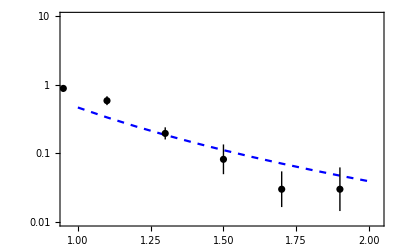

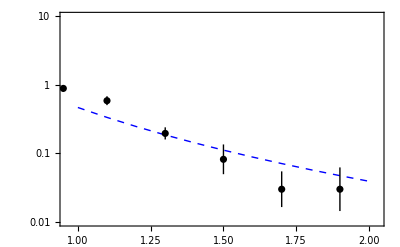

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot14mrw = ListLogPlot[{{{1.,0.46853125339307383},{1.1,0.3357061043505425},{1.2000000000000002,0.24709074486407054},{1.3,0.18613422247806058},{1.4000000000000001,0.14298508926204231},{1.5,0.11167297873162355},{1.6,0.08850575756366443},{1.7000000000000002,0.07107577332348566},{1.8,0.05772309432721048},{1.9000000000000001,0.04734118941084342},{2.,0.03918232003210019}}},Joined->True,PlotStyle->{{Blue,Dashed}},Frame->True,PlotRange-> {{0.96,2.03},{0.01,10}}];
data14=ErrorListLogPlot[{{0.025,6.11,0.49},{0.075,12.11,0.73},{0.125,17.03,0.96},{0.175,18.65,0.81},{0.225,18.28,0.9},{0.275,19.1,0.65},{0.325,16.31,0.83},{0.375,14.19,0.9},{0.425,11.3,0.85},{0.475,9.33,0.48},{0.55,6.73,0.33},{0.65,4.46,0.29},{0.75,2.48,0.19},{0.85,1.69,0.19},{0.95,0.89,0.1},{1.10,0.589,0.088},{1.30,0.196,0.04},{1.50,0.082,0.041},{1.70,0.03,0.018},{1.90,0.03,0.022}},PlotStyle->{Black,Thin}];
Plot14mrw=Show[listforplot14mrw,data14]
```

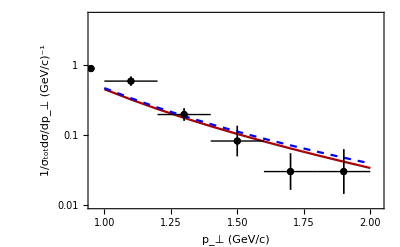

```mathematica
Show[Plot14kmr,Plot14mrw]
```

data of 1/σ_0dσ/dp_t, mu=22; TASSO

```mathematica
SIntegral/.mu2->484/4;
kkk5[kt2_]=%;Clear[result22];result22 = {};
result22 = Flatten[Table[{{0.1j,kkk5[0.1j*0.1j]}},{j,10,30}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0555513486745237}. NIntegrate obtained 22.9256 and 0.00113058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910503}. NIntegrate obtained 23.0665 and 0.0172151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910142}. NIntegrate obtained 22.9511 and 0.0171781 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,0.887108},{1.1,0.647362},{1.2,0.484284},{1.3,0.370181},{1.4,0.28815},{1.5,0.227938},{1.6,0.182775},{1.7,0.148422},{1.8,0.121831},{1.9,0.100954},{2.,0.0844056},{2.1,0.0705928},{2.2,0.0594897},{2.3,0.0504637},{2.4,0.0430891},{2.5,0.0370048},{2.6,0.0319399},{2.7,0.027705},{2.8,0.0241398},{2.9,0.0211203},{3.,0.0185504}}

```mathematica
a22=1;
data22calcmrw=Table[{result22[[i,1]],a22*result22[[i,2]]},{i,1,19,1}]
```

{{1.,0.887108},{1.1,0.647362},{1.2,0.484284},{1.3,0.370181},{1.4,0.28815},{1.5,0.227938},{1.6,0.182775},{1.7,0.148422},{1.8,0.121831},{1.9,0.100954},{2.,0.0844056},{2.1,0.0705928},{2.2,0.0594897},{2.3,0.0504637},{2.4,0.0430891},{2.5,0.0370048},{2.6,0.0319399},{2.7,0.027705},{2.8,0.0241398}}

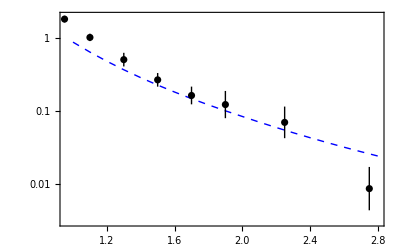

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot22mrw = ListLogPlot[{{{1.,0.8871077350580382},{1.1,0.6473616824132512},{1.2000000000000002,0.4842842836567809},{1.3,0.3701805973170285},{1.4000000000000001,0.28815018440552637},{1.5,0.22793761507163848},{1.6,0.18277514566361877},{1.7000000000000002,0.14842205840033015},{1.8,0.12183118868552868},{1.9000000000000001,0.1009543219176727},{2.,0.08440562918733686},{2.1,0.07059275823618891},{2.2,0.0594896809300175},{2.3000000000000003,0.05046372696970857},{2.4000000000000004,0.04308909144398323},{2.5,0.03700477537384834},{2.6,0.031939903212091045},{2.7,0.02770503696539878},{2.8000000000000003,0.024139793199177167},{3.0,0.018139793199177167}}},Joined->True,PlotStyle->{{Thick,Blue,Dashed}},Frame->True,PlotRange-> {{0.96,2.8},{0.003,2}}];
data22=ErrorListLogPlot[{{0.025,6.79,0.46},{0.075,14.29,0.66},{0.125,18.1,1.},{0.175,21.5,1.1},{0.225,21.58,0.87},{0.275,21.3,1.5},{0.325,18.97,0.75},{0.375,16.7,1.},{0.425,13.71,0.74},{0.475,12.03,0.76},{0.55,8.47,0.44},{0.65,6.02,0.42},{0.75,4.15,0.25},{0.85,2.52,0.29},{0.95,1.84,0.19},{1.1,1.03,0.12},{1.3,0.51,0.11},{1.5,0.269,0.058},{1.7,0.164,0.046},{1.9,0.123,0.053},{2.25,0.07,0.035},{2.75,0.0086,0.0059}},PlotStyle->{Black,Thin},PlotRange-> {{1.0,3.0},{0.0,3.0}}];
Plot22mrw=Show[listforplot22mrw,data22]
```

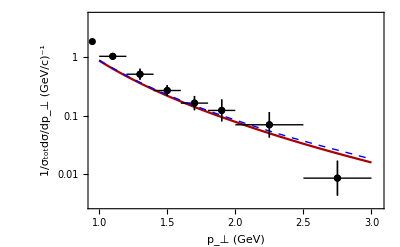

```mathematica
Show[Plot22kmr,Plot22mrw]
```

data of 1/σ_0dσ/dp_t, mu=35; TASSO

```mathematica
SIntegral/.mu2->1225/4;
kkk5[kt2_]=%;
Clear[result35]
result35 = {};
result35 = Flatten[Table[{{0.1j,kkk5[ 0.1j*0.1j]}},{j,10,52}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.942517376804298}. NIntegrate obtained 24.5333 and 0.00925356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.942490137005453}. NIntegrate obtained 25.0078 and 0.0218758 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0945955368455841}. NIntegrate obtained 25.0739 and 0.000912681 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
a35=1;
data35calc=Table[{result35[[i,1]],a35*result35[[i,2]]},{i,1,42,1}]
{{1.,1.6251450924771218},{1.1,1.2102367027143175},{1.2000000000000002,0.9218335854033155},{1.3,0.7162903477288934},{1.4000000000000001,0.5659987342710148},{1.5,0.4538278288834446},{1.6,0.36910648377640043},{1.7000000000000002,0.3034974143811651},{1.8,0.25221473044648673},{1.9000000000000001,0.21150616653128612},{2.,0.17894133906708667},{2.1,0.15071178181918696},{2.2,0.12786219977168722},{2.3000000000000003,0.10916822840109504},{2.4000000000000004,0.09376710693130083},{2.5,0.08099079680599862},{2.6,0.07029854769733863},{2.7,0.06129104307091891},{2.8000000000000003,0.053674860339473024},{2.9000000000000004,0.047192327566523196},{3.,0.04164659976386522},{3.1,0.03701598468010186},{3.2,0.033014861478857446},{3.3000000000000003,0.02954048538859084},{3.4000000000000004,0.02651140883922541},{3.5,0.023861802734876782},{3.6,0.021535982737988117},{3.7,0.019484592053244407},{3.8000000000000003,0.017669086736799972},{3.9000000000000004,0.016061215388352697},{4.,0.014632157081834359},{4.1000000000000005,0.013354474409487276},{4.2,0.012213304707158987},{4.3,0.011191579595527634},{4.4,0.010270411773733796},{4.5,0.009442440524265397},{4.6000000000000005,0.008694708158981353},{4.7,0.008018208686971316},{4.800000000000001,0.007405264900051428},{4.9,0.0068483151797481346},{5.,0.006341707165655401},{5.1000000000000005,0.00588126424839023}}
```

{{1.,1.62515},{1.1,1.21024},{1.2,0.921834},{1.3,0.71629},{1.4,0.565999},{1.5,0.453828},{1.6,0.369106},{1.7,0.303497},{1.8,0.252215},{1.9,0.211506},{2.,0.178941},{2.1,0.150712},{2.2,0.127862},{2.3,0.109168},{2.4,0.0937671},{2.5,0.0809908},{2.6,0.0702985},{2.7,0.061291},{2.8,0.0536749},{2.9,0.0471923},{3.,0.0416466},{3.1,0.037016},{3.2,0.0330149},{3.3,0.0295405},{3.4,0.0265114},{3.5,0.0238618},{3.6,0.021536},{3.7,0.0194846},{3.8,0.0176691},{3.9,0.0160612},{4.,0.0146322},{4.1,0.0133545},{4.2,0.0122133},{4.3,0.0111916},{4.4,0.0102704},{4.5,0.00944244},{4.6,0.00869471},{4.7,0.00801821},{4.8,0.00740526},{4.9,0.00684832},{5.,0.00634171},{5.1,0.00588126}}

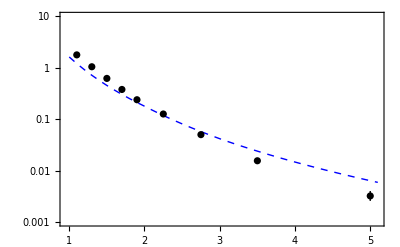

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot35mrw = ListLogPlot[{{{1.,1.6251450924771218},{1.1,1.2102367027143175},{1.2000000000000002,0.9218335854033155},{1.3,0.7162903477288934},{1.4000000000000001,0.5659987342710148},{1.5,0.4538278288834446},{1.6,0.36910648377640043},{1.7000000000000002,0.3034974143811651},{1.8,0.25221473044648673},{1.9000000000000001,0.21150616653128612},{2.,0.17894133906708667},{2.1,0.15071178181918696},{2.2,0.12786219977168722},{2.3000000000000003,0.10916822840109504},{2.4000000000000004,0.09376710693130083},{2.5,0.08099079680599862},{2.6,0.07029854769733863},{2.7,0.06129104307091891},{2.8000000000000003,0.053674860339473024},{2.9000000000000004,0.047192327566523196},{3.,0.04164659976386522},{3.1,0.03701598468010186},{3.2,0.033014861478857446},{3.3000000000000003,0.02954048538859084},{3.4000000000000004,0.02651140883922541},{3.5,0.023861802734876782},{3.6,0.021535982737988117},{3.7,0.019484592053244407},{3.8000000000000003,0.017669086736799972},{3.9000000000000004,0.016061215388352697},{4.,0.014632157081834359},{4.1000000000000005,0.013354474409487276},{4.2,0.012213304707158987},{4.3,0.011191579595527634},{4.4,0.010270411773733796},{4.5,0.009442440524265397},{4.6000000000000005,0.008694708158981353},{4.7,0.008018208686971316},{4.800000000000001,0.007405264900051428},{4.9,0.0068483151797481346},{5.,0.006341707165655401},{5.1000000000000005,0.00588126424839023}}},Joined->True,Frame->True,PlotStyle->{{Thick,Blue,Dashed}},PlotRange-> {{0.96,5.1},{0.001,10}}];
data35=ErrorListLogPlot[{{1.10,1.786,0.054},{1.30,1.049,0.039},{1.50,0.622,0.038},{1.70,0.379,0.019},{1.90,0.239,0.016},{2.25,0.1261,0.0066},{2.75,0.0500,0.0048},{3.5,0.0155,0.0018},{5,0.0032,0.00071}},PlotStyle->{Black,Thin}];
Plot35mrw=Show[listforplot35mrw,data35]
```

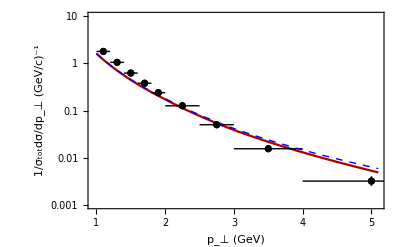

```mathematica
Show[Plot35kmr,Plot35mrw]
```

data of 1/σ_0dσ/dp_t, mu=44; TASSO

```mathematica
(*(4Pi AlphaS[mu2]/(3*mu2))*)
```

```mathematica
SIntegral/.mu2->1936/4;
kkk5[kt2_]=%;
Clear[result44]
result44 = {};
result44 = Flatten[Table[{{0.1j,kkk5[0.1j*0.1j]}},{j,10,50}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.953993832028754}. NIntegrate obtained 25.342 and 0.0113561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.953622622656088}. NIntegrate obtained 26.0402 and 0.0264265 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.954366644752514}. NIntegrate obtained 26.1725 and 0.0195233 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
a44=1;
data44calc=Table[{result44[[i,1]],a44*result44[[i,2]]},{i,1,41,1}]
```

{{1.,2.14957},{1.1,1.61702},{1.2,1.2431},{1.3,0.973893},{1.4,0.775559},{1.5,0.626624},{1.6,0.512755},{1.7,0.424406},{1.8,0.354815},{1.9,0.299397},{2.,0.254749},{2.1,0.21542},{2.2,0.183426},{2.3,0.157158},{2.4,0.135445},{2.5,0.117367},{2.6,0.10217},{2.7,0.0893587},{2.8,0.0784838},{2.9,0.0692044},{3.,0.0612335},{3.1,0.0545561},{3.2,0.04877},{3.3,0.0437374},{3.4,0.039335},{3.5,0.0354807},{3.6,0.0320834},{3.7,0.0290844},{3.8,0.0264315},{3.9,0.0240715},{4.,0.0219681},{4.1,0.0200884},{4.2,0.0184043},{4.3,0.0168927},{4.4,0.015532},{4.5,0.0143042},{4.6,0.0131941},{4.7,0.0121894},{4.8,0.0112756},{4.9,0.0104464},{5.,0.00968959}}

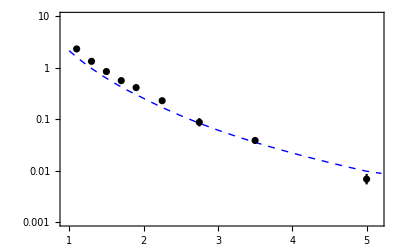

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot44 = ListLogPlot[{{{1.,2.149572552254884},{1.1,1.617021877564976},{1.2000000000000002,1.243099441892129},{1.3,0.9738927192244902},{1.4000000000000001,0.7755591092131039},{1.5,0.6266240654549441},{1.6,0.5127554497203276},{1.7000000000000002,0.4244057969444235},{1.8,0.3548151458802785},{1.9000000000000001,0.29939664486191503},{2.,0.2547489742045316},{2.1,0.21542012967141888},{2.2,0.18342551955402095},{2.3000000000000003,0.15715764243120897},{2.4000000000000004,0.1354448008275529},{2.5,0.1173667687367231},{2.6,0.10216996729928796},{2.7,0.08935874701674708},{2.8000000000000003,0.07848376203403122},{2.9000000000000004,0.06920442460857364},{3.,0.06123345905174357},{3.1,0.05455609529238054},{3.2,0.04877004209528139},{3.3000000000000003,0.04373737933255068},{3.4000000000000004,0.03933504432386044},{3.5,0.03548072661842353},{3.6,0.032083390431506785},{3.7,0.0290843647316456},{3.8000000000000003,0.026431460766753536},{3.9000000000000004,0.02407145056704609},{4.,0.0219680990737535},{4.1000000000000005,0.020088415706871875},{4.2,0.0184043426126381},{4.3,0.01689272185140837},{4.4,0.015532003264491064},{4.5,0.014304175480573578},{4.6000000000000005,0.01319409992152779},{4.7,0.012189368528831113},{4.800000000000001,0.011275562506021922},{4.9,0.01044637741990065},{5.,0.009689594598880934},{5.2,0.008789594598880934}}},Joined->True,Frame->True,PlotStyle->{{Thick,Blue,Dashed}},PlotRange-> {{0.96,5.15},{0.001,10}}];
data44=ErrorListLogPlot[{{1.1,2.334,0.077},{1.30,1.338,0.057},{1.50,0.846,0.044},{1.70,0.563,0.036},{1.90,0.412,0.034},{2.25,0.229,0.016},{2.75,0.087,0.016},{3.5,0.0385,0.005},{5,0.0068,0.0016}},PlotStyle->{Black},PlotRange-> {{0.96,5.1},{0,22.5}}];
Plot44mrw=Show[listforplot44,data44]
```

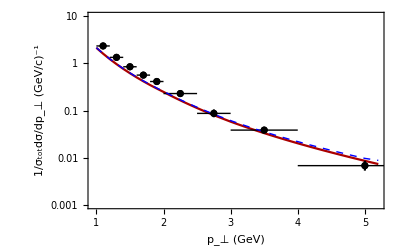

```mathematica
Show[Plot44kmr,Plot44mrw]
```

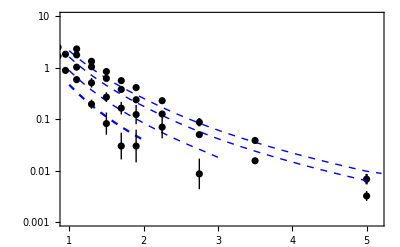

```mathematica
Show[Plot44mrw,Plot14mrw,Plot22mrw,Plot35mrw]
```

data of 1/σ_0dσ/dp_t, mu=29; MARKII

```mathematica
SIntegral/.mu2->841/4;
kkk5[kt2_]=%;Clear[result29];result29 = {};
result29 = Flatten[Table[{{0.1j,kkk5[0.1j*0.1j]}},{j,10,25}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.931333}. NIntegrate obtained 23.8589 and 0.0100975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.932417}. NIntegrate obtained 24.2991 and 0.0188421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.931704}. NIntegrate obtained 24.2206 and 0.0193219 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,1.28002},{1.1,0.945061},{1.2,0.714622},{1.3,0.55148},{1.4,0.433073},{1.5,0.345461},{1.6,0.279242},{1.7,0.22842},{1.8,0.188865},{1.9,0.157623},{2.,0.132704},{2.1,0.111444},{2.2,0.0942604},{2.3,0.0802705},{2.4,0.0687599},{2.5,0.0592403}}

```mathematica
a29=1;
data29calc=Table[{result29[[i,1]],a29*result29[[i,2]]},{i,1,16,1}]
```

{{1.,1.28002},{1.1,0.945061},{1.2,0.714622},{1.3,0.55148},{1.4,0.433073},{1.5,0.345461},{1.6,0.279242},{1.7,0.22842},{1.8,0.188865},{1.9,0.157623},{2.,0.132704},{2.1,0.111444},{2.2,0.0942604},{2.3,0.0802705},{2.4,0.0687599},{2.5,0.0592403}}

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

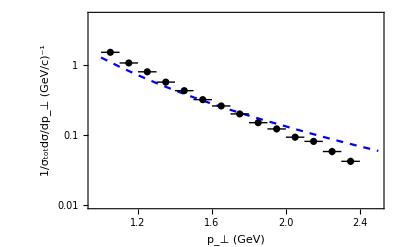

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot29mrw = ListLogPlot[{{{1.,1.2800240662910296},{1.1,0.9450610329065985},{1.2000000000000002,0.7146221004122748},{1.3,0.5514803648627504},{1.4000000000000001,0.4330733303464303},{1.5,0.34546068556815834},{1.6,0.27924240132297007},{1.7000000000000002,0.22842016991244535},{1.8,0.18886522102273393},{1.9000000000000001,0.15762273013282926},{2.,0.13270419505013784},{2.1,0.1114443230505713},{2.2,0.09426040124873888},{2.3000000000000003,0.08027051622625538},{2.4000000000000004,0.06875988976062371},{2.5,0.059240299380804495}}},Joined->True,PlotStyle->{{Blue,Dashed}},Frame->True,PlotStyle->{{Blue,Dashed}},PlotRange-> {{0.96,2.5},{0.01,5}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/σ_totdσ/dp_⊥ (GeV/c)^-1"}];
data29=ErrorListLogPlot[{{{1.05,1.52},ErrorBar[0.05,0.062]},{{1.15,1.07},ErrorBar[0.05,0.045]},{{1.25,0.8},ErrorBar[0.05,0.035]},{{1.35,0.57},ErrorBar[0.05,0.026]},{{1.45,0.43},ErrorBar[0.05,0.024]},{{1.55,0.32},ErrorBar[0.05,0.019]},{{1.65,0.26},ErrorBar[0.05,0.02]},
{{1.75,0.2},ErrorBar[0.05,0.015]},{{1.85,0.15},ErrorBar[0.05,0.015]},{{1.95,0.122},ErrorBar[0.05,0.013]},{{2.05,0.093},ErrorBar[0.05,0.01]},{{2.15,0.081},ErrorBar[0.05,0.009]},{{2.25,0.058},ErrorBar[0.05,0.007]},{{2.35,0.042},ErrorBar[0.05,0.005]}},PlotStyle->{Black,Thin},PlotRange-> {{1.0,10.0},{0.0,3.0}}];
Plot29mrw=Show[listforplot29mrw,data29]
```

data of 1/σ_0dσ/dp_t, mu=52; AMY

```mathematica
SIntegral/.mu2->2970.25/4;
kkk5[kt2_]=%;Clear[result52];result52 = {};
result52 = Flatten[Table[{{0.33j,kkk5[0.33j*0.33j]}},{j,3,17}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.950679555950659}. NIntegrate obtained 28.476 and 0.0517127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.95145829980407}. NIntegrate obtained 28.3868 and 0.0351275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.951187803662063}. NIntegrate obtained 28.0203 and 0.0262937 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.99,6.05775},{1.32,1.22754},{1.65,0.628737},{1.98,0.361595},{2.31,0.215489},{2.64,0.136125},{2.97,0.0901208},{3.3,0.0625455},{3.63,0.044851},{3.96,0.0330223},{4.29,0.0248493},{4.62,0.0190529},{4.95,0.0148477},{5.28,0.0116858},{5.61,0.00931017}}

```mathematica
a52=1;
data52calc=Table[{result52[[i,1]],a52*result52[[i,2]]},{i,1,14,1}]
```

{{0.99,6.05775},{1.32,1.22754},{1.65,0.628737},{1.98,0.361595},{2.31,0.215489},{2.64,0.136125},{2.97,0.0901208},{3.3,0.0625455},{3.63,0.044851},{3.96,0.0330223},{4.29,0.0248493},{4.62,0.0190529},{4.95,0.0148477},{5.28,0.0116858}}

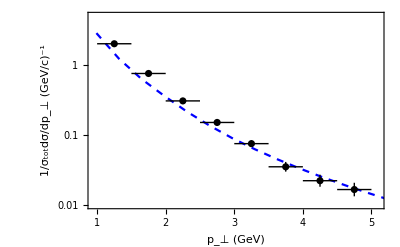

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot52mrw = ListLogPlot[{{{0.99,2.857752909785361},{1.32,1.2275366560822756},{1.6500000000000001,0.6287366699305962},{1.98,0.361594779972111},{2.31,0.2154888223008263},{2.64,0.13612464018814815},{2.97,0.0901207846721021},{3.3000000000000003,0.06254554197307689},{3.6300000000000003,0.04485100428488566},{3.96,0.033022292145970786},{4.29,0.02484934557624384},{4.62,0.019052940651256057},{4.95,0.014847747479212137},{5.28,0.011685827497786332}}},Joined->True,Frame->True,PlotStyle->{{Blue,Dashed}},PlotRange-> {{0.95,5.1},{0.01,5}},FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/σ_totdσ/dp_⊥ (GeV/c)^-1"}];
data52=ErrorListLogPlot[{{{1.25,2.014},ErrorBar[0.25,0.048]},{{1.75,0.757},ErrorBar[0.25,0.028]},{{2.25,0.307},ErrorBar[0.25,0.017]},{{2.75,0.151},ErrorBar[0.25,0.012]},{{3.25,0.0752},ErrorBar[0.25,0.0082]},{{3.75,0.0351},ErrorBar[0.25,0.0056]},{{4.25,0.0222},ErrorBar[0.25,0.0044]},{{4.75,0.0166},ErrorBar[0.25,0.0037]}},PlotStyle->{Black,Thin},PlotRange-> {{1.0,10.0},{0.0,3.0}}];
Plot52mrw=Show[listforplot52mrw,data52]
```

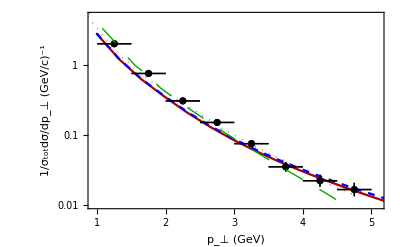

```mathematica
Show[Plot52kmr,Plot52mrw,QCDamylundME,QCDamyPS]
```

data of 1/NdN/dp_t, mu=34; CELLO

```mathematica
(*(4Pi AlphaS[mu2]/(3*mu2))*)
```

```mathematica
SIntegral/.mu2->1156/4;
kkk5[kt2_]=%;
Clear[result34]
result34 = {};
result34 = Flatten[Table[{{0.2j,kkk5[ 0.2j*0.2j]}},{j,5,15}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.940632382738203}. NIntegrate obtained 24.4246 and 0.00900306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0772698215872269}. NIntegrate obtained 24.9072 and 0.00108901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.942486}. NIntegrate obtained 24.9772 and 0.032532 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
a34=0.08;
data34calc=Table[{result34[[i,1]],a34*result34[[i,2]]},{i,1,11,1}]
{{1.,0.12537167116471046},{1.2000000000000002,0.07095353186665969},{1.4000000000000001,0.04347610421028362},{1.6,0.02829550293556472},{1.8,0.019307813756194038},{2.,0.013676228120699971},{2.2,0.009764328578164847},{2.4000000000000004,0.007155731693027704},{2.6,0.005359131634908706},{2.8000000000000003,0.004089127238415195},{3.,0.0031703557085353603}}
```

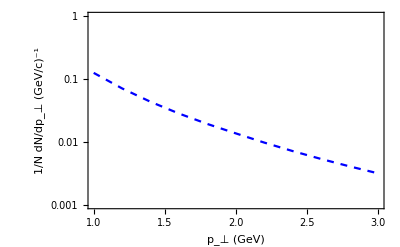

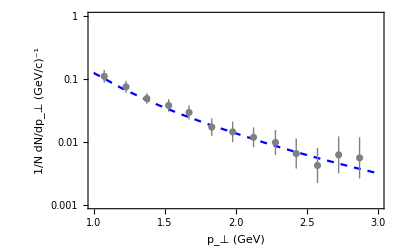

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot34 = ListLogPlot[{{{1.,0.12537167116471046},{1.2000000000000002,0.07095353186665969},{1.4000000000000001,0.04347610421028362},{1.6,0.02829550293556472},{1.8,0.019307813756194038},{2.,0.013676228120699971},{2.2,0.009764328578164847},{2.4000000000000004,0.007155731693027704},{2.6,0.005359131634908706},{2.8000000000000003,0.004089127238415195},{3.,0.0031703557085353603}}},Joined->True,PlotStyle->{{Blue,Dashed}},PlotRange-> {{1.0,3.0},{0.001,1}},Frame-> True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/N dN/dp_⊥ (GeV/c)^-1"}];

Plotmrw34=Show[listforplot34]
```

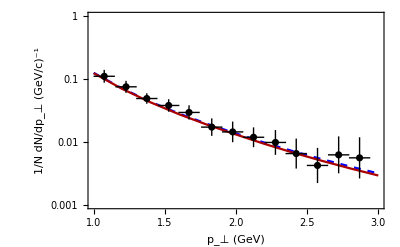

```mathematica
Show[Plotmrw34,Plotkmr34]
```

data of 1/σ_0dσ/dp_t^2, mu=14; TASSO

```mathematica
SIntegrant[z_]=0.0018 mu2^0.727*(2*Pi)/kt2*UDtotal[z,mu2,kt2]/z;
Subscript[z, 0]=a;b=(0.8);a=0.05;n=100;step=(b-a)/n;Do[Subscript[z, i]=Subscript[z, i-1]+step,{i,1,n}];SIntegral=(b-a)*(1/(3*n)(SIntegrant[Subscript[z, 0]]+4*∑_(i=1)^(n/2) SIntegrant[Subscript[z, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant[Subscript[z, 2i]]+SIntegrant[Subscript[z, n]]));
```

```mathematica
SIntegral/.mu2->14^2/4;
kkk5[kt2_]=%;
Clear[resuresult34mrwlt14]
result14mrw = {};
result14mrw = Flatten[Table[{{0.2*j,kkk5[0.2j]}},{j,5,26}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0555513486745237}. NIntegrate obtained 21.3401 and 0.00108154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.857544}. NIntegrate obtained 21.2231 and 0.0132802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.858033}. NIntegrate obtained 20.8884 and 0.0112893 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.,0.468531},{1.2,0.31095},{1.4,0.219514},{1.6,0.162146},{1.8,0.124041},{2.,0.0975215},{2.2,0.0783836},{2.4,0.0641875},{2.6,0.0533655},{2.8,0.0449843},{3.,0.0383434},{3.2,0.0330075},{3.4,0.0286592},{3.6,0.0250775},{3.8,0.0220974},{4.,0.0195912},{4.2,0.0174414},{4.4,0.0156105},{4.6,0.0140382},{4.8,0.0126806},{5.,0.0115001},{5.2,0.0104688}}

```mathematica
a14t=0.4;
data14tcalcmrw=Table[{result14mrw[[i,1]],a14t*result14mrw[[i,2]]},{i,1,21,1}]
```

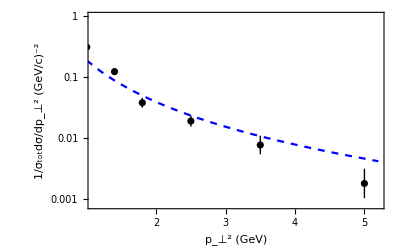

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot14 = ListLogPlot[{{{1.,0.18741250135722953},{1.2000000000000002,0.12438011173283488},{1.4000000000000001,0.08780542685002778},{1.6,0.06485839099871445},{1.8,0.04961655237459697},{2.,0.03900858205478},{2.2,0.031353442230559934},{2.4000000000000004,0.0256749997548568},{2.6,0.021346203312720732},{2.8000000000000003,0.017993733770309422},{3.,0.015337367711680018},{3.2,0.013202981684783406},{3.4000000000000004,0.011463666189150476},{3.6,0.010030982641595583},{3.8000000000000003,0.008838958650261816},{4.,0.007836464006420038},{4.2,0.006976572716350798},{4.4,0.006244211019213231},{4.6000000000000005,0.005615272287075314},{4.800000000000001,0.005072228562414406},{5.,0.004600040434418979},{5.2,0.00416}}},Joined->True,PlotStyle->{{Blue,Dashed}},PlotRange-> {{1.1,5.2},{0.0008,1.0}},Frame->True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥^2 (GeV)","1/σ_totdσ/dp_⊥^2 (GeV/c)^-2"}];
data14pt2=ErrorListLogPlot[{{1.0,0.31,0.021},{1.4,0.123,0.013},{1.8,0.038,0.007},{2.5,0.019,0.004},{3.5,0.0077,0.0027},{5.0,0.0018,0.001}},PlotStyle->{Black,Thin}];
Plot14pt2mrw=Show[listforplot14,data14pt2]
```

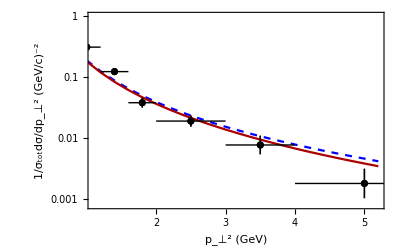

```mathematica
Show[Plot14pt2mrw,Plot14pt2kmr]
```

data of 1/σ_0dσ/dp_t^2, mu=22; TASSO

```mathematica
SIntegral/.mu2->22^2/4;
kkk5[kt2_]=%;
Clear[result22mrw]
result22mrw = {};
result22mrw = Flatten[Table[{{0.2*j,kkk5[0.2* j]}},{j,5,35}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0555513486745237}. NIntegrate obtained 22.9256 and 0.00113058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910503}. NIntegrate obtained 23.0665 and 0.0172151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910142}. NIntegrate obtained 22.9511 and 0.0171781 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,0.887108},{1.2,0.599116},{1.4,0.429095},{1.6,0.320879},{1.8,0.248055},{2.,0.196898},{2.2,0.159585},{2.4,0.131759},{2.6,0.110391},{2.8,0.0936454},{3.,0.0803414},{3.2,0.0695738},{3.4,0.060759},{3.6,0.0534644},{3.8,0.047362},{4.,0.0422028},{4.2,0.0376706},{4.4,0.0337951},{4.6,0.0304619},{4.8,0.0275731},{5.,0.0250539},{5.2,0.0228446},{5.4,0.0209031},{5.6,0.0191892},{5.8,0.0176635},{6.,0.0163021},{6.2,0.0150852},{6.4,0.0139905},{6.6,0.0130043},{6.8,0.012113},{7.,0.0113049}}

```mathematica
a22t=0.4;
data22tcalc=Table[{result22mrw[[i,1]],a22t*result22mrw[[i,2]]},{i,2,31,1}]
```

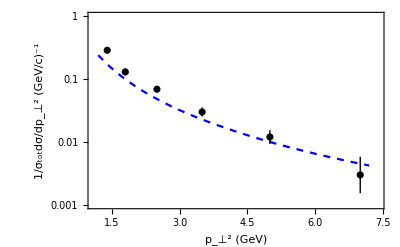

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot22pt2 = ListLogPlot[{{{1.2000000000000002,0.23964622555309534},{1.4000000000000001,0.1716379856696817},{1.6,0.1283514164827687},{1.8,0.0992219196492658},{2.,0.07875934508016018},{2.2,0.06383394262166622},{2.4000000000000004,0.05270359820491526},{2.6,0.0441563312574303},{2.8000000000000003,0.03745814073046828},{3.,0.03213654589035284},{3.2,0.02782953784435448},{3.4000000000000004,0.024303583879882025},{3.6,0.021385759675745786},{3.8000000000000003,0.01894481884412252},{4.,0.016881125837467374},{4.2,0.015068231296220933},{4.4,0.013518040516512298},{4.6000000000000005,0.012184760699648835},{4.800000000000001,0.011029239913484661},{5.,0.01002157983604628},{5.2,0.009137840007778354},{5.4,0.008361237555251647},{5.6000000000000005,0.0076756758628021135},{5.800000000000001,0.007065415473749559},{6.,0.006520835068929396},{6.2,0.006034079611461684},{6.4,0.0055961864286456905},{6.6000000000000005,0.0052017010199894315},{6.800000000000001,0.004845203998142017},{7.,0.004521965035114285},{7.2,0.004221965035114285}}},Joined->True,PlotStyle->{{Blue,Dashed}},PlotRange-> {{1.1,7.4},{0.001,1.0}},Frame->True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥^2 (GeV)","1/σ_totdσ/dp_⊥^2 (GeV/c)^-1"}];
data22pt2=ErrorListLogPlot[{{1.4,0.287,0.025},{1.8,0.13,0.016},{2.5,0.069,0.008},{3.5,0.03,0.005},{5.0,0.012,0.003},{7.0,0.003,0.002}},PlotStyle->{Black,Thin}];
Plot22pt2mrw=Show[listforplot22pt2,data22pt2]
```

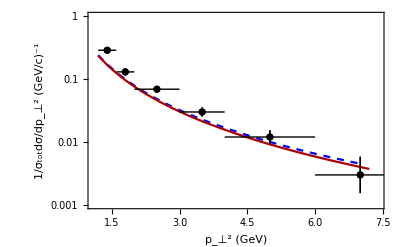

```mathematica
Show[Plot22pt2mrw,Plot22pt2kmr]
```

data of 1/σ_0dσ/dp_t^2, mu=34; TASSO

```mathematica
SIntegral/.mu2->1156/4;
kkk5[kt2_]=%;
Clear[result34]
result34 = {};
result34 = Flatten[Table[{{1*j,kkk5[1* j]}},{j,1,36}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.940632382738203}. NIntegrate obtained 24.4246 and 0.00900306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0772698215872269}. NIntegrate obtained 24.9072 and 0.00108901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.942486}. NIntegrate obtained 24.9772 and 0.032532 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
a34t=0.5;
data34tcalc=Table[{result34[[i,1]],a34t*result34[[i,2]]},{i,1,35,1}]
```

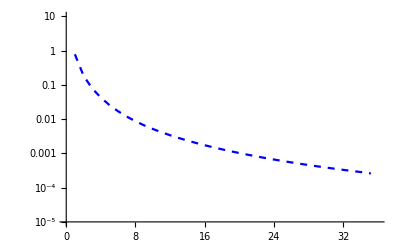

```mathematica
Needs["ErrorBarLogPlots`"]
listforplot34 = ListLogPlot[{{{1,0.7835729447794404},{2,0.18601090617508143},{3,0.07896197690853417},{4,0.04273821287718741},{5,0.025756219293534048},{6,0.016962890352642687},{7,0.011882191493062836},{8,0.008706785783885278},{9,0.006604907726115335},{10,0.005182379548087144},{11,0.004158368277525433},{12,0.003398780474452281},{13,0.002821693466525658},{14,0.0023739422590597008},{15,0.0020201869343092426},{16,0.0017360127884455076},{17,0.001505366662661941},{18,0.0013156212277717382},{19,0.0011574606390157875},{20,0.0010248192978488209},{21,0.0009124085281516306},{22,0.0008165766138337194},{23,0.0007341561795923461},{24,0.0006628471334354772},{25,0.0006008591292303167},{26,0.000546759290585787},{27,0.0004992917725109746},{28,0.0004574152385156261},{29,0.0004202609102354933},{30,0.0003872248343522508},{31,0.00035775258129114724},{32,0.0003312875443775803},{33,0.0003074895593519092},{34,0.0002860253674920333},{35,0.0002666039040290634},{35.2,0.0002566039040290634}}},Joined->True,PlotStyle->{{Blue,Dashed}},PlotRange-> {{0.0,36},{0.00001,10.0}}];
data34pt2=ErrorListLogPlot[{{1.4,0.57,0.011},{1.8,0.32,0.008},{2.5,0.15,0.004},{3.5,0.066,0.002},{5.0,0.026,0.001},{7.0,0.0098,0.0006},{9.0,0.0049,0.0004},{11,0.0023,0.0003},{13,0.0013,0.0003},{15,0.0011,0.0002},{17,0.00055,0.00018},{19,0.00029,0.00013},{25,0.0002,0.00009},{35,0.00003,0.00002}},PlotStyle->{Green,Thick}];
Plot34pt2mrw=Show[listforplot34]
```

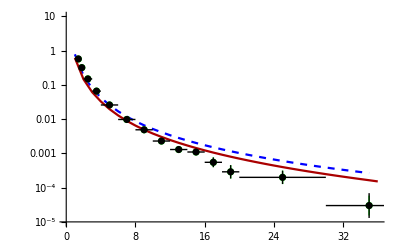

```mathematica
Show[Plot34pt2mrw,Plot34pt2kmr]
```

data of 1/σ_0dσ/dx, mu=14; TASSO

```mathematica
SIntegrant[kt2_]=29.94/mu2^0.47 UDtotal[z,mu2,kt2]/kt2/z;
Subscript[kt2, 0]=a;b=(0.9999mu2);a=1;n=100;step=(b-a)/n;Do[Subscript[kt2, i]=Subscript[kt2, i-1]+step,{i,1,n}];SIntegral=(b-a)*(1/(3*n)(SIntegrant[Subscript[kt2, 0]]+4*∑_(i=1)^(n/2) SIntegrant[Subscript[kt2, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant[Subscript[kt2, 2i]]+SIntegrant[Subscript[kt2, n]]));
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
SIntegral/.mu2->(196/4);
kkk5[z_]=%;
Clear[result14z]
result14z = {};
result14z = Flatten[Table[{{0.1j,kkk5[0.1 j]}},{j,1,7}],1]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.857603}. NIntegrate obtained 20.2377 and 0.0127088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.118099905255562}. NIntegrate obtained 10.9895 and 0.0000458869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.801353}. NIntegrate obtained 19.3147 and 0.0105053 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.1,51.2597},{0.2,17.3594},{0.3,7.57033},{0.4,3.57408},{0.5,1.70049},{0.6,0.762121},{0.7,0.291648}}

```mathematica
Clear[result14z1]
result14z1 = {};
result14z1 = Flatten[Table[{{0.01j,kkk5[0.01 j]}},{j,2,9}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.858344}. NIntegrate obtained 21.6418 and 0.0083614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0315584034385769200692362090876486035995185375213623046875}. NIntegrate obtained 36.7778 and 0.000311409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.800922}. NIntegrate obtained 25.9155 and 0.0100286 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.02,372.153},{0.03,228.778},{0.04,161.866},{0.05,123.927},{0.06,99.0672},{0.07,81.8118},{0.08,68.9899},{0.09,59.1033}}

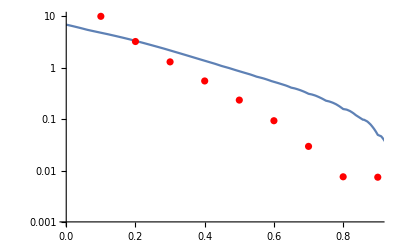

```mathematica
a14z=1;
data14zcalc=Table[{result14z[[i,1]],a14z*result14z[[i,2]]},{i,1,9,1}];
Aa=LogPlot[Dhtotal[z,196/4],{z,0,1},PlotRange->{{0,0.9},{0.001,10}}];
Bb=ListLogPlot[data14zcalc,PlotRange->{{0,1},{0.001,10}},PlotStyle->Red];
Show[Aa,Bb]
```

{{0.1,41.0078},{0.2,13.8875},{0.3,6.05626},{0.4,2.85927},{0.5,1.36039},{0.6,0.609697},{0.7,0.233318}}

Part::partw: Part 9 of {{0.02,372.153},{0.03,228.778},{0.04,161.866},{0.05,123.927},{0.06,99.0672},{0.07,81.8118},{0.08,68.9899},{0.09,59.1033}} does not exist.

{{0.02,297.722},{0.03,183.022},{0.04,129.493},{0.05,99.1417},{0.06,79.2538},{0.07,65.4494},{0.08,55.1919},{0.09,47.2827},{{{0.02,372.153},{0.03,228.778},{0.04,161.866},{0.05,123.927},{0.06,99.0672},{0.07,81.8118},{0.08,68.9899},{0.09,59.1033}}⟦9,1⟧,0.8 {{0.02,372.153},{0.03,228.778},{0.04,161.866},{0.05,123.927},{0.06,99.0672},{0.07,81.8118},{0.08,68.9899},{0.09,59.1033}}⟦9,2⟧}}

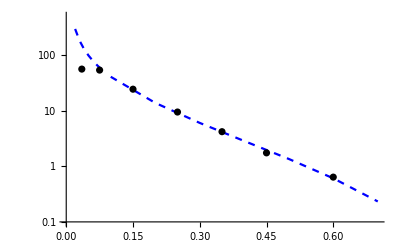

```mathematica
a14z=0.8;
data14zcalc=Table[{result14z[[i,1]],a14z*result14z[[i,2]]},{i,1,7,1}]
data14zcalc1=Table[{result14z1[[i,1]],a14z*result14z1[[i,2]]},{i,1,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot14z = ListLogPlot[{data14zcalc1,data14zcalc},PlotStyle->{{Blue,Dashed}},Joined->True,PlotRange-> {{0.0,0.7},{0.1,500}}];
data14z=ErrorListLogPlot[{{0.025,47.2,0.015},{0.035,56.5,0.45},{0.045,66.3,0.008},{0.055,62.9,0.004},{0.07,58.0,0.002},{0.09,44.9,0.001},{0.11,36.1,0.0006},{0.13,29.4,0.0004},{0.15,22.05,0.0003},{0.17,18.9,0.0003},{0.19,16.01,0.0002},{0.225,11.58,0.00018},{0.275,7.44,0.00013},{0.325,5.28,0.00009},{0.375,3.15,0.00002},{0.425,1.75,0.015},{0.55,0.95,0.45},{0.65,0.342,0.008},{0.75,0.181,0.004},{0.9,0.058,0.002}},PlotStyle->{{Black,Thin}},PlotRange-> {{0,1},{0,100}}];
data14z1=ErrorListLogPlot[{{0.035,56.4,3.9},{0.075,54.1,1.7},{0.15,24.51,0.46},{0.25,9.51,0.28},{0.35,4.21,0.22},{0.45,1.75,0.11},{0.6,0.64,0.061}},PlotStyle->{{Black,Thin}},PlotRange-> {{0,1},{0.01,100}}];
Plot14zmrw=Show[listforplot14z,data14z1]
```

data of 1/σ_0dσ/dx, mu=22; TASSO

```mathematica
SIntegral/.mu2->484/4;
kkk5[z_]=%;
Clear[result22z]
result22z = {};
result22z = Flatten[Table[{{0.1j,kkk5[0.1 j]}},{j,1,7}],1]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910338}. NIntegrate obtained 22.4933 and 0.0173695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.118099905255562}. NIntegrate obtained 10.1798 and 0.0000165834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.832994}. NIntegrate obtained 21.5767 and 0.0134261 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.1,37.1498},{0.2,13.1456},{0.3,5.84867},{0.4,2.80786},{0.5,1.37995},{0.6,0.656739},{0.7,0.275884}}

```mathematica
SIntegral/.mu2->484/4;
kkk5[z_]=%;
Clear[result22z1]
result22z1= {};
result22z1 = Flatten[Table[{{0.01j,kkk5[0.01 j]}},{j,2,10}],1]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.910024}. NIntegrate obtained 22.8782 and 0.0108917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.03419725523152030051410310562687300262041389942169189453125}. NIntegrate obtained 37.9318 and 0.0000862208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.833461}. NIntegrate obtained 34.7058 and 0.00688144 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.02,251.96},{0.03,156.234},{0.04,111.525},{0.05,86.1687},{0.06,69.7128},{0.07,57.9817},{0.08,49.2898},{0.09,42.5467},{0.1,37.1498}}

{{0.1,40.8647},{0.2,14.4601},{0.3,6.43354},{0.4,3.08865},{0.5,1.51794},{0.6,0.722413},{0.7,0.303472}}

{{0.03,171.857},{0.04,122.678},{0.05,94.7856},{0.06,76.6841},{0.07,63.7799},{0.08,54.2188},{0.09,46.8013},{0.1,40.8647}}

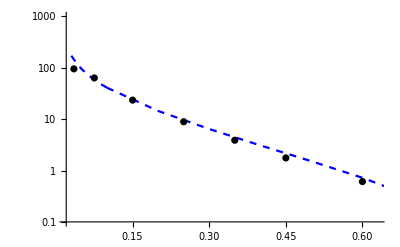

```mathematica
a22z=1.1;
data22zcalc=Table[{result22z[[i,1]],a22z*result22z[[i,2]]},{i,1,7,1}]
data22zcalc1=Table[{result22z1[[i,1]],a22z*result22z1[[i,2]]},{i,2,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot22z = ListLogPlot[{data22zcalc1,data22zcalc},PlotStyle->{{Blue,Dashed}},Joined->True,PlotRange-> {{0.02,0.63},{0.1,1000}}];
data22z1=ErrorListLogPlot[{{0.035,95.4,3.9},{0.075,63.6,1.7},{0.15,23.48,0.46},{0.25,8.92,0.28},{0.35,3.89,0.22},{0.45,1.76,0.11},{0.6,0.61,0.061}},PlotStyle->{{Black,Thin}}];
Plot22zmrw=Show[listforplot22z,data22z1]
```

data of 1/σ_0dσ/dx, mu=35; TASSO

```mathematica
SIntegral/.mu2->1225/4;
kkk5[z_]=%;
Clear[result35z]
result35z = {};
result35z = Flatten[Table[{{0.1j,kkk5[0.1 j]}},{j,1,7}],1];
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.943736}. NIntegrate obtained 24.8482 and 0.0354959 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.118099905255562}. NIntegrate obtained 9.44078 and 0.0000199157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.848814}. NIntegrate obtained 22.7428 and 0.017734 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
SIntegral/.mu2->1225/4;
kkk5[z_]=%;
Clear[result35z1]
result35z1= {};
result35z1 = Flatten[Table[{{0.01j,kkk5[0.01 j]}},{j,2,9}],1]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.942708303497203}. NIntegrate obtained 24.187 and 0.00945608 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.03419725523152030051410310562687300262041389942169189453125}. NIntegrate obtained 38.3312 and 0.0000627363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.848774}. NIntegrate obtained 43.0156 and 0.0203152 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.02,194.404},{0.03,122.96},{0.04,89.2605},{0.05,70.1259},{0.06,57.8088},{0.07,48.8395},{0.08,42.0775},{0.09,36.798}}

{{0.1,32.4773},{0.2,12.3805},{0.3,5.7424},{0.4,2.84906},{0.5,1.46037},{0.6,0.744558},{0.7,0.349703}}

Part::partw: Part 9 of {{0.02,194.404},{0.03,122.96},{0.04,89.2605},{0.05,70.1259},{0.06,57.8088},{0.07,48.8395},{0.08,42.0775},{0.09,36.798}} does not exist.

{{0.03,122.96},{0.04,89.2605},{0.05,70.1259},{0.06,57.8088},{0.07,48.8395},{0.08,42.0775},{0.09,36.798},{{{0.02,194.404},{0.03,122.96},{0.04,89.2605},{0.05,70.1259},{0.06,57.8088},{0.07,48.8395},{0.08,42.0775},{0.09,36.798}}⟦9,1⟧,{{0.02,194.404},{0.03,122.96},{0.04,89.2605},{0.05,70.1259},{0.06,57.8088},{0.07,48.8395},{0.08,42.0775},{0.09,36.798}}⟦9,2⟧}}

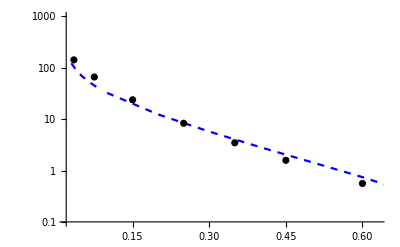

```mathematica
a35z=1;
data35zcalc=Table[{result35z[[i,1]],a35z*result35z[[i,2]]},{i,1,7,1}]
data35zcalc1=Table[{result35z1[[i,1]],a35z*result35z1[[i,2]]},{i,2,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot35z = ListLogPlot[{data35zcalc1,data35zcalc},PlotStyle->{{Blue,Dashed}},Joined->True,PlotRange-> {{0.02,0.63},{0.1,1000}}];
data35z1=ErrorListLogPlot[{{0.035,142.9,3.9},{0.075,66.23,1.7},{0.15,23.85,0.46},{0.25,8.33,0.28},{0.35,3.47,0.22},{0.45,1.58,0.11},{0.6,0.56,0.061}},PlotStyle->{{Black,Thin}}];
Plot35zmrw=Show[listforplot35z,data35z1]
```

data of 1/σ_0dσ/dx, mu=44; TASSO

```mathematica
SIntegral/.mu2->1936/4;
kkk5[z_]=%;
Clear[result44z]
result44z = {};
result44z = Flatten[Table[{{0.1j,kkk5[0.1 j]}},{j,1,7}],1]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.953275368795361}. NIntegrate obtained 26.0286 and 0.0412032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.85233}. NIntegrate obtained 22.9682 and 0.013579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.79608}. NIntegrate obtained 20.3743 and 0.0147733 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,33.6374},{0.2,13.4239},{0.3,6.38417},{0.4,3.2298},{0.5,1.69333},{0.6,0.889823},{0.7,0.436857}}

```mathematica
Clear[result44z1]
result44z1 = {};
result44z1 = Flatten[Table[{{0.01j,kkk5[0.01 j]}},{j,2,10}],1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.953717676348559}. NIntegrate obtained 24.8447 and 0.0116474 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0315584034385769200692362090876486035995185375213623046875}. NIntegrate obtained 38.3047 and 0.0000718571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.852602}. NIntegrate obtained 47.3829 and 0.0188662 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.02,183.073},{0.03,118.092},{0.04,87.0407},{0.05,69.2417},{0.06,57.5975},{0.07,49.3776},{0.08,42.9686},{0.09,37.9293},{0.1,33.6374}}

{{0.1,33.6374},{0.2,13.4239},{0.3,6.38417},{0.4,3.2298},{0.5,1.69333},{0.6,0.889823},{0.7,0.436857}}

{{0.03,118.092},{0.04,87.0407},{0.05,69.2417},{0.06,57.5975},{0.07,49.3776},{0.08,42.9686},{0.09,37.9293},{0.1,33.6374}}

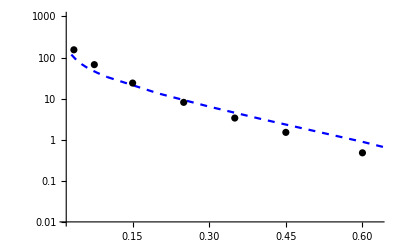

```mathematica
a44z=1;
data44zcalc=Table[{result44z[[i,1]],a44z*result44z[[i,2]]},{i,1,7,1}]
data44zcalc1=Table[{result44z1[[i,1]],a44z*result44z1[[i,2]]},{i,2,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot44z = ListLogPlot[{data44zcalc1,data44zcalc},PlotStyle->{{Blue,Dashed}},Joined->True,PlotRange-> {{0.02,0.63},{0.01,1000}}];
data44z=ErrorListLogPlot[{{0.025,47.2,0.015},{0.035,56.5,0.45},{0.045,66.3,0.008},{0.055,95.9,2.7},{0.07,70.5,1.3},{0.09,49.0,1.7},{0.11,37.17,0.89},{0.13,28.67,0.84},{0.15,22.66,0.61},{0.17,17.79,0.76},{0.19,13.45,0.47},{0.225,10.06,0.32},{0.275,6.18,0.23},{0.325,4.08,0.18},{0.375,2.66,0.14},{0.425,1.517,0.072},{0.55,0.631,0.052},{0.65,0.331,0.031},{0.75,0.129,0.017},{0.9,0.03,0.0059}},PlotStyle->{Green,Thick},PlotRange-> {{0,1},{0,100}}];
data44z1=ErrorListLogPlot[{{0.035,154.4,3.9},{0.075,67.2,1.7},{0.15,23.95,0.46},{0.25,8.12,0.28},{0.35,3.37,0.22},{0.45,1.51,0.11},{0.6,0.48,0.061}},PlotStyle->{{Black,Thin}}];
Plot44zmrw=Show[listforplot44z,data44z1]
```

<pt2> for PLUTTO

```mathematica
SIntegrant[z_]=1/kt2*UDtotal[z,mu2,kt2];
Subscript[z, 0]=a;b=(0.9);a=0.05;n=30;step=(b-a)/n;Do[Subscript[z, i]=Subscript[z, i-1]+step,{i,1,n}];SIntegral=(b-a)*(1/(3*n)(SIntegrant[Subscript[z, 0]]+4*∑_(i=1)^(n/2) SIntegrant[Subscript[z, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant[Subscript[z, 2i]]+SIntegrant[Subscript[z, n]]));
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
SIntegrant14[kt2_]:=SIntegral;
Subscript[kt2, 0]=a;b=(Sqrt[mu2]);a=1.0;n=30;step=(b-a)/n;Do[Subscript[kt2, i]=Subscript[kt2, i-1]+step,{i,1,n}];SIntegral14:=(b-a)*(1/(3*n)(SIntegrant14[Subscript[kt2, 0]]+4*∑_(i=1)^(n/2) SIntegrant14[Subscript[kt2, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant14[Subscript[kt2, 2i]]+SIntegrant14[Subscript[kt2, n]]));

SIntegrant140[kt2_]:=SIntegral*Sqrt[kt2];
Subscript[kt2, 0]=a;b=(Sqrt[mu2]);a=1.0;n=30;step=(b-a)/n;Do[Subscript[kt2, i]=Subscript[kt2, i-1]+step,{i,1,n}];SIntegral140:=(b-a)*(1/(3*n)(SIntegrant140[Subscript[kt2, 0]]+4*∑_(i=1)^(n/2) SIntegrant140[Subscript[kt2, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant140[Subscript[kt2, 2i]]+SIntegrant140[Subscript[kt2, n]]));
```

```mathematica
pt2avrage7mrw=(SIntegral140/.mu2-> 7.7^2/4)/(SIntegral14/.mu2-> 7.7^2/4)
pt2avrage9mrw=(SIntegral140/.mu2-> 9.4^2/4)/(SIntegral14/.mu2-> 9.4^2/4)
pt2avrage12mrw=(SIntegral140/.mu2-> 12^2/4)/(SIntegral14/.mu2-> 12^2/4)
pt2avrage13mrw=(SIntegral140/.mu2-> 13^2/4)/(SIntegral14/.mu2-> 13^2/4)
pt2avrage17mrw=(SIntegral140/.mu2-> 17^2/4)/(SIntegral14/.mu2-> 17^2/4)
pt2avrage27mrw=(SIntegral140/.mu2-> 27^2/4)/(SIntegral14/.mu2-> 27^2/4)
pt2avrage30mrw=(SIntegral140/.mu2-> 30.6^2/4)/(SIntegral14/.mu2-> 30.6^2/4)
```

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.53316

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.65574

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.82626

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.88749

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

2.11391

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

2.59211

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

2.74341

```mathematica
pt2avrage14mrw=(SIntegral140/.mu2-> 196/4)/(SIntegral14/.mu2->  196/4)
pt2avrage22mrw=(SIntegral140/.mu2-> 484/4)/(SIntegral14/.mu2-> 484/4)
pt2avrage25mrw=(SIntegral140/.mu2-> 25^2/4)/(SIntegral14/.mu2-> 25^2/4)
pt2avrage35mrw=(SIntegral140/.mu2->1225/4)/(SIntegral14/.mu2-> 1225/4)
pt2avrage41mrw=(SIntegral140/.mu2->41^2/4)/(SIntegral14/.mu2-> 41^2/4)
pt2avrage44mrw=(SIntegral140/.mu2-> 1936/4)/(SIntegral14/.mu2-> 1936/4)
```

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

2.91748

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

3.24408

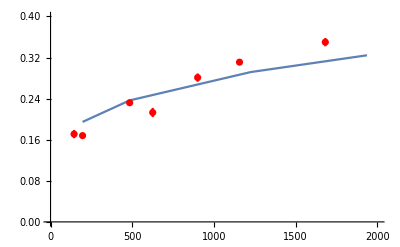

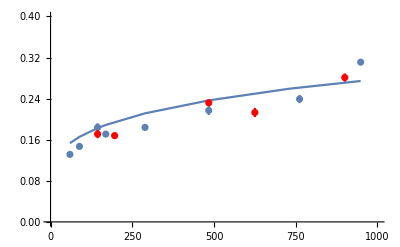

```mathematica
atasso=0.025/2;
Needs["ErrorBarLogPlots`"]
pt2avrage=ListPlot[{{196,1/10pt2avrage14mrw},{484,1/10pt2avrage22mrw},{1225,1/10pt2avrage35mrw},{1936,1/10pt2avrage44mrw}},PlotRange->{{0,2000},{0,0.4}},Joined->True];
pt2avrageplutto=ListPlot[{{7.7^2,1/10pt2avrage7mrw},{9.4^2,1/10pt2avrage9mrw},{12^2,1/10pt2avrage12mrw},{13^2,1/10pt2avrage13mrw},{17^2,1/10pt2avrage17mrw},{484,1/10pt2avrage22mrw},{27^2,1/10pt2avrage27mrw},{30.8^2,1/10pt2avrage30mrw}},PlotRange->{{0,1000},{0,0.4}},Joined->True];
datapt2avrage=ErrorListPlot[{{12^2,0.171,0.008},{196,0.168,0.002},{484,0.232,0.004},{25^2,0.213,0.009},{900,0.281,0.008},{1156,0.311,0.002},{41^2,0.35,0.008}},PlotStyle->{Red}];
datapt2avrageplutto=ErrorListPlot[{{7.7^2,0.1314,0.0033},{9.4^2,0.147,0.0048},{12^2,0.184,0.008},{13^2,0.171,0.002},{17^2,0.184,0.004},{22^2,0.217,0.009},{27.6^2,0.2392,0.008},{30.8^2,0.311,0.002}}];
Show[pt2avrage,datapt2avrage]
Show[pt2avrageplutto,datapt2avrageplutto,datapt2avrage]
```

data of 1/NdN/dp_t, mu=34; CELLO

```mathematica
SIntegrant[z_]=(2*Pi)/Sqrt[kt2]*UDtotal[z,mu2,kt2];
Subscript[z, 0]=a;b=(0.9);a=0.05;n=50;step=(b-a)/n;Do[Subscript[z, i]=Subscript[z, i-1]+step,{i,1,n}];SIntegral=(b-a)*(1/(3*n)(SIntegrant[Subscript[z, 0]]+4*∑_(i=1)^(n/2) SIntegrant[Subscript[z, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant[Subscript[z, 2i]]+SIntegrant[Subscript[z, n]]));
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
SIntegral/.mu2->1156/4;
kkk5[kt2_]=%;
Clear[result34]
result34 = {};
result34 = Flatten[Table[{{0.5j,kkk5[ 0.5j*0.5j]}},{j,1,5}],1]
```

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = 0.0588235 (17.-1. √kt2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{0.5,19.2366},{1.,2.11621},{1.5,0.496338},{2.,0.168271},{2.5,0.0706233}}

NIntegrate::nlim: x = 0.0588235 (17.-1. √kt2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{0.5,0.0288548},{1.,0.00317432},{1.5,0.000744506},{2.,0.000252407},{2.5,0.000105935}}

{{0.5,0.192366},{1.,0.0211621},{1.5,0.00496338},{2.,0.00168271},{2.5,0.000706233}}

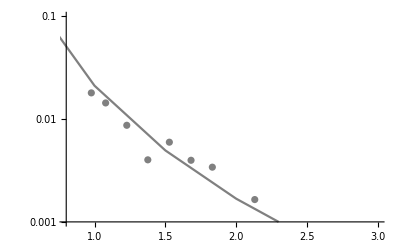

```mathematica
a34=0.01;
data34calc=Table[{result34[[i,1]],a34*result34[[i,2]]},{i,1,5,1}]
Needs["ErrorBarLogPlots`"]
listforplot34 = ListLogPlot[{data34calc},Joined->True,PlotStyle->{Gray},PlotRange-> {{0.8,3.0},{0.001,0.1}}];
data34=ListLogPlot[{{0.97721,0.01803},{1.07828,0.01439},{1.22763,0.00872},{1.37615,0.00402},{1.52823,0.00597},{1.68138,0.00398},{1.83179,0.00341},{2.13133,0.00165}},PlotStyle->{Thick,Gray},PlotRange-> {{0.8,3.0},{0,0.05}}];
Plot34cellomrw=Show[listforplot34,data34]
```

```mathematica
data34tasso=ListLogPlot[{{0.97681,0.15797},{1.07397,0.11071},{1.22719,0.07534},{1.37325,0.04909},{1.52686,0.03805},{1.66994,0.02950},{1.82971,0.01724},{1.97654,0.01447},{2.12331,0.01189},{2.27712,0.00984},{2.42325,0.00655},{2.57280,0.00424},{2.72135,0.00625},{2.86839,0.00560}},PlotStyle->{Thick,Gray},PlotRange-> {{0.8,5.1},{0,2.5}}];
```

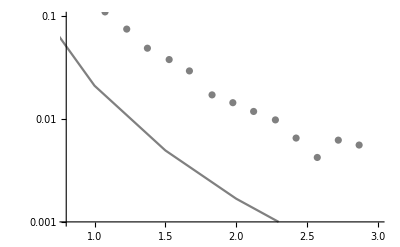

```mathematica
Plot6=Show[listforplot34,data34tasso]
```

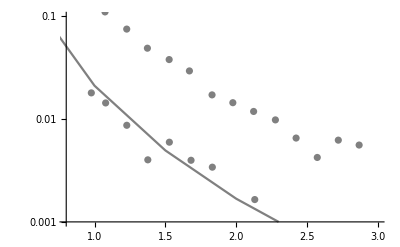

```mathematica
Plot6=Show[listforplot34,data34tasso,data34]
```

data of 1/σ_0dσ/dp_t^2, mu=34; TASSO

```mathematica
SIntegrant[z_]=1/kt2*UDtotal[z,mu2,kt2];
Subscript[z, 0]=a;b=(0.9);a=0.05;n=100;step=(b-a)/n;Do[Subscript[z, i]=Subscript[z, i-1]+step,{i,1,n}];SIntegral=(b-a)*(1/(3*n)(SIntegrant[Subscript[z, 0]]+4*∑_(i=1)^(n/2) SIntegrant[Subscript[z, 2i-1]]+2*∑_(i=1)^(n/2-1) SIntegrant[Subscript[z, 2i]]+SIntegrant[Subscript[z, n]]));
SIntegral/.mu2->1156/4;
kkk5[kt2_]=%;
Clear[result34]
result34 = {};
result34 = Flatten[Table[{{1*j,kkk5[1* j]}},{j,1,40}],1]
```

NIntegrate::nlim: x = z is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = (-1. √kt2+√mu2)/(√mu2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: x = 0.0588235 (17.-1. √kt2) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{1,6.73591},{2,1.38672},{3,0.533891},{4,0.2678},{5,0.155679},{6,0.0994631},{7,0.067866},{8,0.0486071},{9,0.0361349},{10,0.0276684},{11,0.0217003},{12,0.0173616},{13,0.0141252},{14,0.0116579},{15,0.00974135},{16,0.00822829},{17,0.00701665},{18,0.00603413},{19,0.00522843},{20,0.00456109},{21,0.00400334},{22,0.00353335},{23,0.00313436},{24,0.00279332},{25,0.00250001},{26,0.00224628},{27,0.00202563},{28,0.00183279},{29,0.00166349},{30,0.00151422},{31,0.00138209},{32,0.00126469},{33,0.00116001},{34,0.00106638},{35,0.000982351},{36,0.000906733},{37,0.000838493},{38,0.000776749},{39,0.000720746},{40,0.000669829}}

{{1,0.673591},{2,0.138672},{3,0.0533891},{4,0.02678},{5,0.0155679},{6,0.00994631},{7,0.0067866},{8,0.00486071},{9,0.00361349},{10,0.00276684},{11,0.00217003},{12,0.00173616},{13,0.00141252},{14,0.00116579},{15,0.000974135},{16,0.000822829},{17,0.000701665},{18,0.000603413},{19,0.000522843},{20,0.000456109},{21,0.000400334},{22,0.000353335},{23,0.000313436},{24,0.000279332},{25,0.000250001},{26,0.000224628},{27,0.000202563},{28,0.000183279},{29,0.000166349},{30,0.000151422},{31,0.000138209},{32,0.000126469},{33,0.000116001},{34,0.000106638},{35,0.0000982351},{36,0.0000906733},{37,0.0000838493},{38,0.0000776749},{39,0.0000720746}}

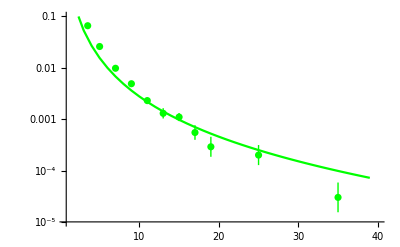

```mathematica
a34t=0.1;
data34tcalc=Table[{result34[[i,1]],a34t*result34[[i,2]]},{i,1,39,1}]
Needs["ErrorBarLogPlots`"]
listforplot34t = ListLogPlot[{data34tcalc},Joined->True,PlotStyle->{Green},PlotRange-> {{0.8,40},{0.00001,0.1}}];
data34t=ErrorListLogPlot[{{1.0,1.18,0.015},{1.4,0.57,0.45},{1.8,0.32,0.008},{2.5,0.15,0.004},{3.5,0.066,0.002},{5.0,0.026,0.001},{7.0,0.0098,0.0006},{9.0,0.0049,0.0004},{11,0.0023,0.0003},{13,0.0013,0.0003},{15,0.0011,0.0002},{17,0.00055,0.00018},{19,0.00029,0.00013},{25,0.0002,0.00009},{35,0.00003,0.00002}},PlotStyle->{Green,Thick}];
Plot7mrw=Show[listforplot34t,data34t]
```

data of 1/σ_0dσ/dp_t, mu=14; TASSO max

```mathematica
SIntegral/.mu2->2*196;
kkk5[kt2_]=%;Clear[result14];result14 = {};
result14 = Flatten[Table[{{0.5j,kkk5[0.5j*0.5j]}},{j,2,4}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.949725}. NIntegrate obtained -0.0243052 and 0.0000186146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.949708}. NIntegrate obtained 0.0414301 and 0.000083666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.949849}. NIntegrate obtained 0.128499 and 0.000140537 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,0.939086},{1.5,0.208838},{2.,0.0699849}}

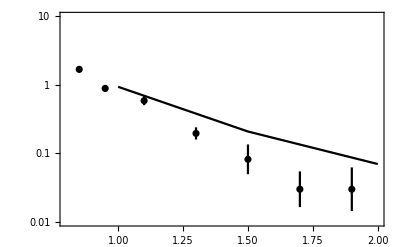

```mathematica
data14calcmax=Table[{result14[[i,1]],a14*result14[[i,2]]},{i,1,3,1}]
Needs["ErrorBarLogPlots`"]
listforplot14 = ListLogPlot[{data14calcmax},Joined->True,PlotStyle->{Black,Thick},Frame->True,PlotRange-> {{0.8,2.0},{0.01,10}}];
data14=ErrorListLogPlot[{{0.025,6.11,0.49},{0.075,12.11,0.73},{0.125,17.03,0.96},{0.175,18.65,0.81},{0.225,18.28,0.9},{0.275,19.1,0.65},{0.325,16.31,0.83},{0.375,14.19,0.9},{0.425,11.3,0.85},{0.475,9.33,0.48},{0.55,6.73,0.33},{0.65,4.46,0.29},{0.75,2.48,0.19},{0.85,1.69,0.19},{0.95,0.89,0.1},{1.10,0.589,0.088},{1.30,0.196,0.04},{1.50,0.082,0.041},{1.70,0.03,0.018},{1.90,0.03,0.022}},PlotStyle->{Black}];
Plot14mrwmax=Show[listforplot14,data14]
```

data of 1/σ_0dσ/dp_t, mu=22; TASSO

```mathematica
SIntegral/.mu2->2*484;
kkk5[kt2_]=%;Clear[result22];result22 = {};
result22 = Flatten[Table[{{0.5j,kkk5[0.5j*0.5j]}},{j,2,6}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.968029}. NIntegrate obtained 0.0151943 and 0.0000569175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.967966}. NIntegrate obtained 0.122347 and 0.000218092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.968224}. NIntegrate obtained 0.239356 and 0.000229102 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,1.75602},{1.5,0.410519},{2.,0.142411},{2.5,0.0615439},{3.,0.0307101}}

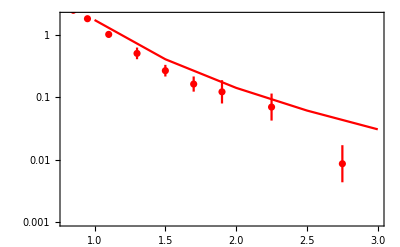

```mathematica
data22calcmax=Table[{result22[[i,1]],a22*result22[[i,2]]},{i,1,5,1}]
Needs["ErrorBarLogPlots`"]
listforplot22 = ListLogPlot[{data22calcmax},Joined->True,PlotStyle->{Red,Thick},Frame->True,PlotRange-> {{0.8,3.0},{0.001,2}}];
data22=ErrorListLogPlot[{{0.025,6.79,0.46},{0.075,14.29,0.66},{0.125,18.1,1.},{0.175,21.5,1.1},{0.225,21.58,0.87},{0.275,21.3,1.5},{0.325,18.97,0.75},{0.375,16.7,1.},{0.425,13.71,0.74},{0.475,12.03,0.76},{0.55,8.47,0.44},{0.65,6.02,0.42},{0.75,4.15,0.25},{0.85,2.52,0.29},{0.95,1.84,0.19},{1.1,1.03,0.12},{1.3,0.51,0.11},{1.5,0.269,0.058},{1.7,0.164,0.046},{1.9,0.123,0.053},{2.25,0.07,0.035},{2.75,0.0086,0.0059}},PlotStyle->{Red},PlotRange-> {{1.0,3.0},{0.0,3.0}}];
Plot22mrwmax=Show[listforplot22,data22]
```

data of 1/σ_0dσ/dp_t, mu=35; TASSO

```mathematica
SIntegral/.mu2->2*1225;
kkk5[kt2_]=%;
Clear[result35]
result35 = {};
result35 = Flatten[Table[{{0.5j,kkk5[ 0.5j*0.5j]}},{j,2,10}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.979881}. NIntegrate obtained -0.0387855 and 0.0000362048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.979889}. NIntegrate obtained 0.0740748 and 0.000130282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.979818}. NIntegrate obtained 0.217352 and 0.000261986 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,2.2342},{1.5,0.549483},{2.,0.197497},{2.5,0.0877708},{3.,0.0448202},{3.5,0.0252051},{4.,0.0152115},{4.5,0.00967768},{5.,0.00641543}}

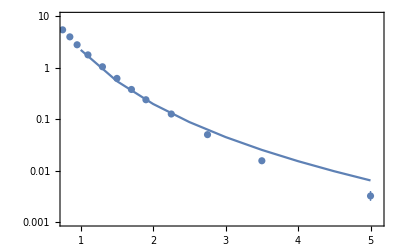

```mathematica
data35calcmax=Table[{result35[[i,1]],a35*result35[[i,2]]},{i,1,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot35 = ListLogPlot[{data35calcmax},Joined->True,Frame->True,PlotStyle->{DarkerGreen},PlotRange-> {{0.8,5.1},{0.001,10}}];
data35=ErrorListLogPlot[{{0.025,7.7,0.38},{0.075,16.43,0.45},{0.125,21.96,0.41},{0.175,24.96,0.46},{0.225,25.43,0.45},{0.275,23.95,0.36},{0.325,21.88,0.29},{0.375,19.13,0.56},{0.425,16.5,0.24},{0.475,14.35,0.22},{0.55,11.04,0.16},{0.65,7.73,0.14},{0.75,5.49,0.1},{0.85,4.008,0.085},{0.95,2.81,0.077},{1.10,1.786,0.054},{1.30,1.049,0.039},{1.50,0.622,0.038},{1.70,0.379,0.019},{1.90,0.239,0.016},{2.25,0.1261,0.0066},{2.75,0.0500,0.0048},{3.5,0.0155,0.0018},{5,0.0032,0.00071}},PlotStyle->{DarkerGreen,Thick}];
Plot35mrwmax=Show[listforplot35,data35]
```

data of 1/σ_0dσ/dp_t, mu=44; TASSO

```mathematica
(*(4Pi AlphaS[mu2]/(3*mu2))*)
```

```mathematica
SIntegral/.mu2->2*1936;
kkk5[kt2_]=%;
Clear[result44]
result44 = {};
result44 = Flatten[Table[{{0.5j,kkk5[ 0.5j*0.5j]}},{j,2,10}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.983983}. NIntegrate obtained -0.0255571 and 0.0000496923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.984014}. NIntegrate obtained 0.10812 and 0.000319076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.983982}. NIntegrate obtained 0.265527 and 0.000496199 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,2.94878},{1.5,0.742632},{2.,0.271531},{2.5,0.122337},{3.,0.063139},{3.5,0.0358389},{4.,0.0218098},{4.5,0.0139777},{5.,0.0093349}}

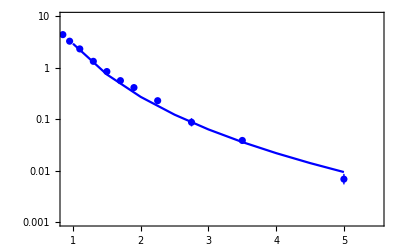

```mathematica
data44calcmax=Table[{result44[[i,1]],a44*result44[[i,2]]},{i,1,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot44 = ListLogPlot[{data44calcmax},Joined->True,Frame->True,PlotStyle->{Blue},PlotRange-> {{0.9,5.5},{0.001,10}}];
data44=ErrorListLogPlot[{{0.025,8.5,0.49},{0.075,17.7,0.92},{0.125,23.19,0.62},{0.175,25.54,0.64},{0.225,26.08,0.67},{0.275,24.,0.56},{0.325,22.69,0.6},{0.375,19.48,0.58},{0.425,17.94,0.59},{0.475,15.02,0.45},{0.55,12.17,0.28},{0.65,8.69,0.22},{0.75,6.27,0.23},{0.85,4.43,0.25},{0.95,3.3,0.16},{1.1,2.334,0.077},{1.30,1.338,0.057},{1.50,0.846,0.044},{1.70,0.563,0.036},{1.90,0.412,0.034},{2.25,0.229,0.016},{2.75,0.087,0.016},{3.5,0.0385,0.005},{5,0.0068,0.0016}},PlotStyle->{Thick,Blue},PlotRange-> {{0.0,5.1},{0,22.5}}];
Plot44mrwmax=Show[listforplot44,data44]
```

MIN

```mathematica
SIntegral/.mu2->196/2;
kkk5[kt2_]=%;Clear[result14];result14 = {};
result14 = Flatten[Table[{{0.5j,kkk5[0.5j*0.5j]}},{j,2,4}],1];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.899193}. NIntegrate obtained -0.0276457 and 0.0000153482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.899317}. NIntegrate obtained 0.00695755 and 0.0000348693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.899356}. NIntegrate obtained 0.0590778 and 0.000101375 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.,0.693857},{1.5,0.143501},{2.,0.0458844}}

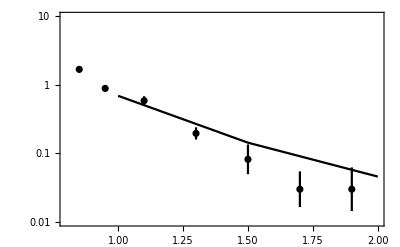

```mathematica
data14calcmin=Table[{result14[[i,1]],a14*result14[[i,2]]},{i,1,3,1}]
Needs["ErrorBarLogPlots`"]
listforplot14 = ListLogPlot[{data14calcmin},Joined->True,PlotStyle->{Black,Thick},Frame->True,PlotRange-> {{0.8,2.0},{0.01,10}}];
data14=ErrorListLogPlot[{{0.025,6.11,0.49},{0.075,12.11,0.73},{0.125,17.03,0.96},{0.175,18.65,0.81},{0.225,18.28,0.9},{0.275,19.1,0.65},{0.325,16.31,0.83},{0.375,14.19,0.9},{0.425,11.3,0.85},{0.475,9.33,0.48},{0.55,6.73,0.33},{0.65,4.46,0.29},{0.75,2.48,0.19},{0.85,1.69,0.19},{0.95,0.89,0.1},{1.10,0.589,0.088},{1.30,0.196,0.04},{1.50,0.082,0.041},{1.70,0.03,0.018},{1.90,0.03,0.022}},PlotStyle->{Black}];
Plot14mrwmin=Show[listforplot14,data14]
```

data of 1/σ_0dσ/dp_t, mu=22; TASSO

```mathematica
SIntegral/.mu2->484/2;
kkk5[kt2_]=%;Clear[result22];result22 = {};
result22 = Flatten[Table[{{0.5j,kkk5[0.5j*0.5j]}},{j,2,6}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.935803}. NIntegrate obtained -0.0352098 and 0.0000130797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.935935}. NIntegrate obtained 0.00886299 and 0.0000392131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.936067}. NIntegrate obtained 0.0796299 and 0.0000742452 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,1.40232},{1.5,0.303762},{2.,0.0999599},{2.5,0.0414606},{3.,0.0200476}}

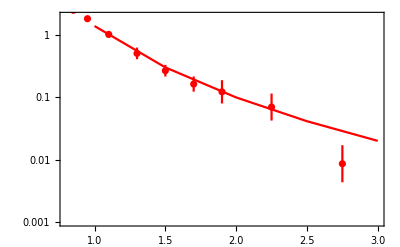

```mathematica
data22calcmin=Table[{result22[[i,1]],a22*result22[[i,2]]},{i,1,5,1}]
Needs["ErrorBarLogPlots`"]
listforplot22 = ListLogPlot[{data22calcmin},Joined->True,PlotStyle->{Red,Thick},Frame->True,PlotRange-> {{0.8,3.0},{0.001,2}}];
data22=ErrorListLogPlot[{{0.025,6.79,0.46},{0.075,14.29,0.66},{0.125,18.1,1.},{0.175,21.5,1.1},{0.225,21.58,0.87},{0.275,21.3,1.5},{0.325,18.97,0.75},{0.375,16.7,1.},{0.425,13.71,0.74},{0.475,12.03,0.76},{0.55,8.47,0.44},{0.65,6.02,0.42},{0.75,4.15,0.25},{0.85,2.52,0.29},{0.95,1.84,0.19},{1.1,1.03,0.12},{1.3,0.51,0.11},{1.5,0.269,0.058},{1.7,0.164,0.046},{1.9,0.123,0.053},{2.25,0.07,0.035},{2.75,0.0086,0.0059}},PlotStyle->{Red},PlotRange-> {{1.0,3.0},{0.001,10.0}}];
Plot22kmrmin=Show[listforplot22,data22]
```

data of 1/σ_0dσ/dp_t, mu=35; TASSO

```mathematica
SIntegral/.mu2->1225/2;
kkk5[kt2_]=%;
Clear[result35]
result35 = {};
result35 = Flatten[Table[{{0.5j,kkk5[ 0.5j*0.5j]}},{j,2,10}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.959779}. NIntegrate obtained -0.00742179 and 0.0000425546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.959638}. NIntegrate obtained 0.0788944 and 0.000146175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.959802}. NIntegrate obtained 0.179889 and 0.000360466 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,1.92706},{1.5,0.439246},{2.,0.1497},{2.5,0.0637983},{3.,0.0314786},{3.5,0.0172081},{4.,0.010135},{4.5,0.00630428},{5.,0.00409298}}

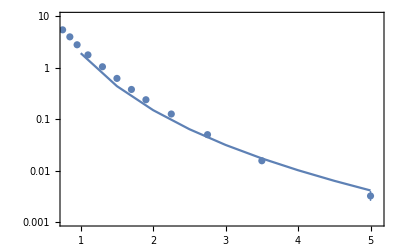

```mathematica
data35calcmin=Table[{result35[[i,1]],a35*result35[[i,2]]},{i,1,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot35 = ListLogPlot[{data35calcmin},Joined->True,Frame->True,PlotStyle->{DarkerGreen},PlotRange-> {{0.8,5.1},{0.001,10}}];
data35=ErrorListLogPlot[{{0.025,7.7,0.38},{0.075,16.43,0.45},{0.125,21.96,0.41},{0.175,24.96,0.46},{0.225,25.43,0.45},{0.275,23.95,0.36},{0.325,21.88,0.29},{0.375,19.13,0.56},{0.425,16.5,0.24},{0.475,14.35,0.22},{0.55,11.04,0.16},{0.65,7.73,0.14},{0.75,5.49,0.1},{0.85,4.008,0.085},{0.95,2.81,0.077},{1.10,1.786,0.054},{1.30,1.049,0.039},{1.50,0.622,0.038},{1.70,0.379,0.019},{1.90,0.239,0.016},{2.25,0.1261,0.0066},{2.75,0.0500,0.0048},{3.5,0.0155,0.0018},{5,0.0032,0.00071}},PlotStyle->{DarkerGreen,Thick}];
Plot35mrwmin=Show[listforplot35,data35]
```

data of 1/σ_0dσ/dp_t, mu=44; TASSO

```mathematica
SIntegral/.mu2->1936/2;
kkk5[kt2_]=%;
Clear[result44]
result44 = {};
result44 = Flatten[Table[{{0.5j,kkk5[ 0.5j*0.5j]}},{j,2,10}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.968029}. NIntegrate obtained 0.0151943 and 0.0000569175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.967966}. NIntegrate obtained 0.122347 and 0.000218092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.968224}. NIntegrate obtained 0.239356 and 0.000229102 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1.,2.63403},{1.5,0.615779},{2.,0.213616},{2.5,0.0923158},{3.,0.0460652},{3.5,0.025413},{4.,0.0150832},{4.5,0.00944678},{5.,0.00617246}}

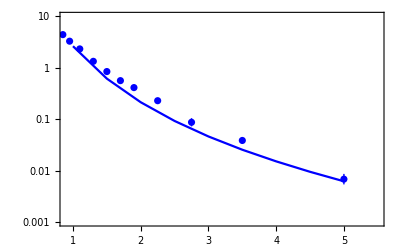

```mathematica
data44calcmin=Table[{result44[[i,1]],a44*result44[[i,2]]},{i,1,9,1}]
Needs["ErrorBarLogPlots`"]
listforplot44 = ListLogPlot[{data44calcmin},Joined->True,Frame->True,PlotStyle->{Blue},PlotRange-> {{0.9,5.5},{0.001,10}}];
data44=ErrorListLogPlot[{{0.025,8.5,0.49},{0.075,17.7,0.92},{0.125,23.19,0.62},{0.175,25.54,0.64},{0.225,26.08,0.67},{0.275,24.,0.56},{0.325,22.69,0.6},{0.375,19.48,0.58},{0.425,17.94,0.59},{0.475,15.02,0.45},{0.55,12.17,0.28},{0.65,8.69,0.22},{0.75,6.27,0.23},{0.85,4.43,0.25},{0.95,3.3,0.16},{1.1,2.334,0.077},{1.30,1.338,0.057},{1.50,0.846,0.044},{1.70,0.563,0.036},{1.90,0.412,0.034},{2.25,0.229,0.016},{2.75,0.087,0.016},{3.5,0.0385,0.005},{5,0.0068,0.0016}},PlotStyle->{Thick,Blue},PlotRange-> {{0.0,5.1},{0,22.5}}];
Plot44mrwmin=Show[listforplot44,data44]
```

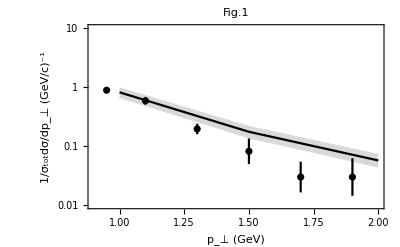

```mathematica
plotmrw14=ListLogPlot[{data14calcmin,data14calcmax},PlotStyle->{{ LightGray,Thickness[0.005]},{ LightGray,Thickness[0.005]}},Filling-> {1->{2}},FillingStyle-> LightGray,Frame-> True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/σ_totdσ/dp_⊥ (GeV/c)^-1"},Joined->True,RotateLabel->True,PlotRange->{{0.9,2},{0.01,10}},PlotLabel->"Fig.1",LabelStyle->Directive[Black]];
Show[plotmrw14,Plot14mrw]
```

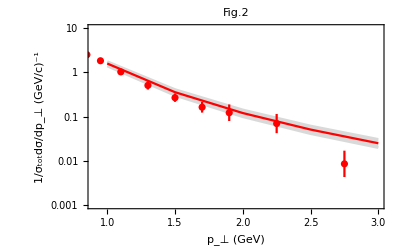

```mathematica
plotmrw22=ListLogPlot[{data22calcmin,data22calcmax},PlotStyle->{{ LightGray,Thickness[0.005]},{ LightGray,Thickness[0.005]}},Filling-> {1->{2}},FillingStyle-> LightGray,Frame-> True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/σ_totdσ/dp_⊥ (GeV/c)^-1"},Joined->True,RotateLabel->True,PlotRange->{{0.9,3},{0.001,10}},PlotLabel->"Fig.2",LabelStyle->Directive[Black]];
Show[plotmrw22,Plot22mrw]
```

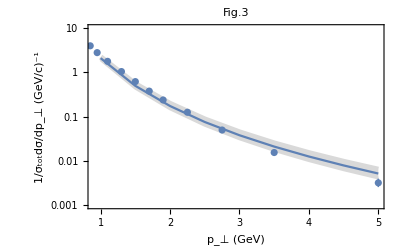

```mathematica
plotmrw35=ListLogPlot[{data35calcmin,data35calcmax},PlotStyle->{{LightGray,Thickness[0.005]},{ LightGray,Thickness[0.01]}},Filling-> {1->{2}},FillingStyle-> LightGray,Frame-> True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/σ_totdσ/dp_⊥ (GeV/c)^-1"},Joined->True,RotateLabel->True,PlotRange->{{0.9,5},{0.001,10}},PlotLabel->"Fig.3",LabelStyle->Directive[Black]];
Show[plotmrw35,Plot35mrw]
```

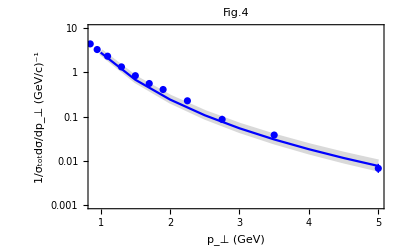

```mathematica
plotmrw44=ListLogPlot[{data44calcmin,data44calcmax},PlotStyle->{{ LightGray,Thickness[0.005]},{ LightGray,Thickness[0.01]}},Filling-> {1->{2}},FillingStyle-> LightGray,Frame-> True,FrameStyle->Directive[Black],FrameLabel->{"p_⊥ (GeV)","1/σ_totdσ/dp_⊥ (GeV/c)^-1"},Joined->True,RotateLabel->True,PlotRange->{{0.9,5},{0.001,10}},PlotLabel->"Fig.4",LabelStyle->Directive[Black]];
Show[plotmrw44,Plot44mrw]
```

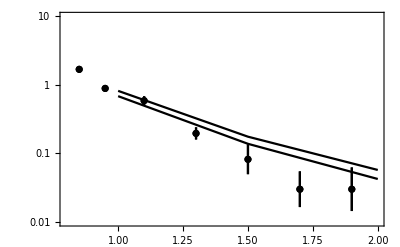

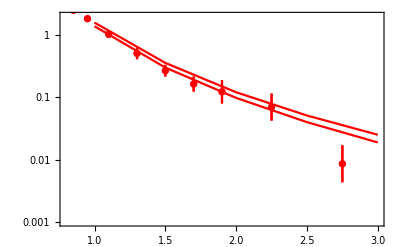

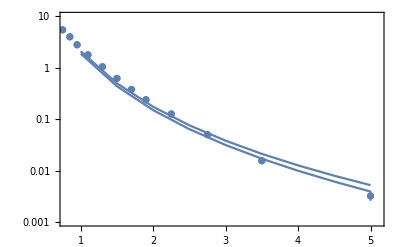

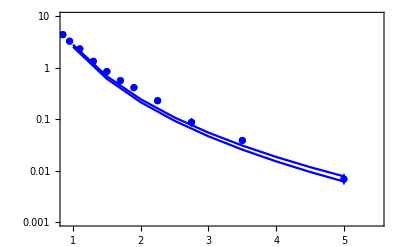

```mathematica
Show[Plot14mrw,Plot14kmr]
Show[Plot22mrw,Plot22kmr]
Show[Plot35mrw,Plot35kmr]
Show[Plot44mrw,Plot44kmr]
```